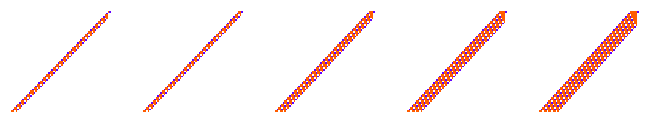

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]]&/@ [[{1}]]
```

```mathematica
[[{1}]]
```

{<|Rule→{7543256137557,3,1},Fitness→-15|>}

```mathematica
{7543256137557,3,1}
```

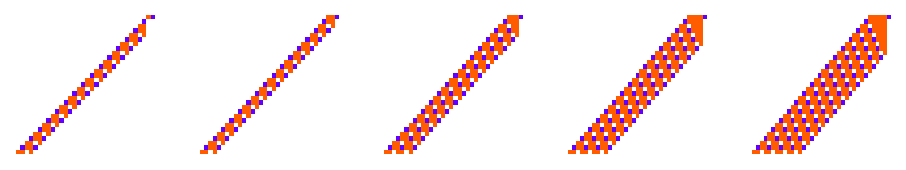

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[{7543256137557,3,1},{Append[Table[1, i], 2], 0}, 30], {i, 5}]]
```

```mathematica
SeedRandom[221130 + 23];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>]
```

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[[[-1, "Rule"]],{Append[Table[1, i], 2], 0}, 60], {i, 5}]]
```

-Graphics-

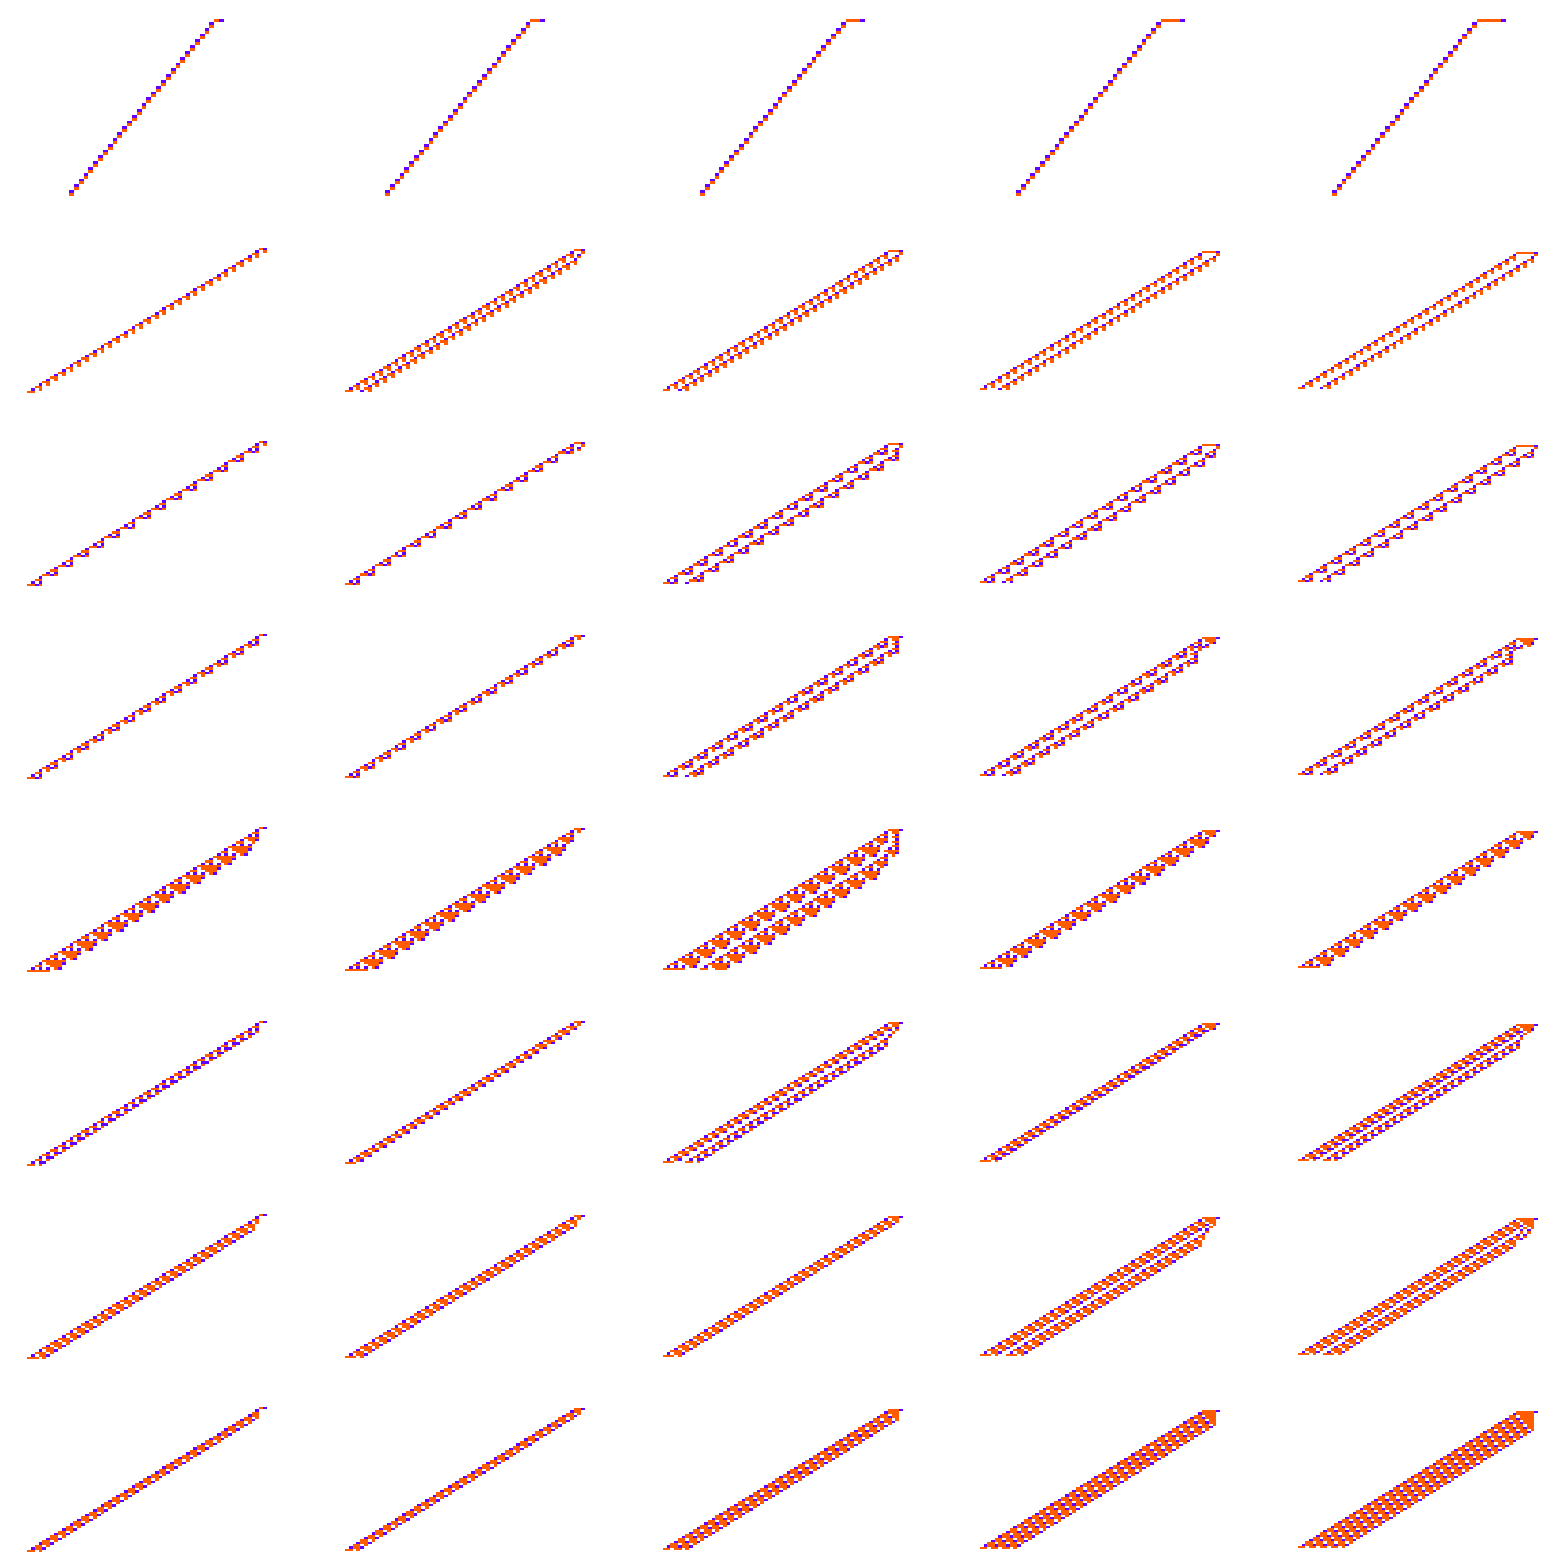

```mathematica
GraphicsGrid[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]&/@ GatherBy[, #Fitness&][[2;;, 1]]]
```

```mathematica
ResourceFunction["ProgressiveMaxPositions"][[[All, "Fitness"]]]
```

{1,5,14,17,74,81,95,98,478}

```mathematica
ListStepPlot[MapIndexed[Block[{ca = CellularAutomaton[#Rule,{Append[Table[1, 5], 2], 0}, 60], loss}, 
loss = Abs[Count[Last[ca], 1] - 9];If[MemberQ[, Last[#2]], Callout[loss, ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}], LabelVisibility->All], loss]]&,], PlotRange->All, LabelingSize->50]
```

-Graphics-

```mathematica
GraphicsGrid[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]&/@ GatherBy[, #Fitness&][[2;;, 1]]]
```

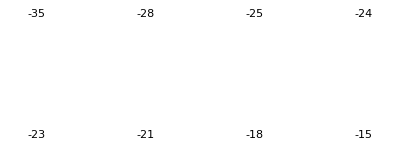

```mathematica
GraphicsGrid[Partition[Labeled[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&@CellularAutomaton[#Rule,{Append[Table[1, 5], 2], 0}, 60], #Fitness]&/@ GatherBy[, #Fitness&][[2;;, 1]], 4]]
```

```mathematica
5
```

```mathematica
GraphicsRow[Labeled[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}], Count[Last[#], 1]]&@CellularAutomaton[#Rule,{Append[Table[1, 5], 2], 0}, 60]&/@ GatherBy[, #Fitness&][[2;;, 1]]]
```

-Graphics-

### Running based on count of 1s

```mathematica
ParallelTable[SeedRandom[221190 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>], {i , 30}]
```

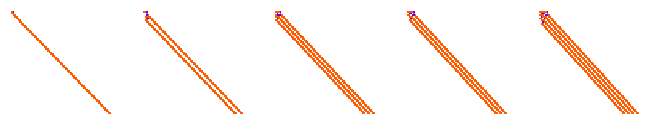
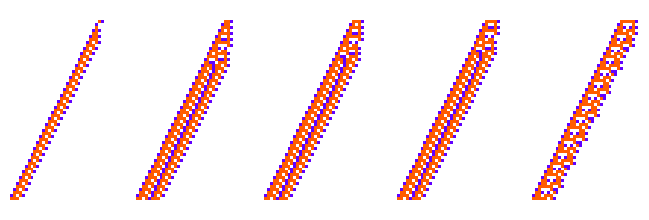
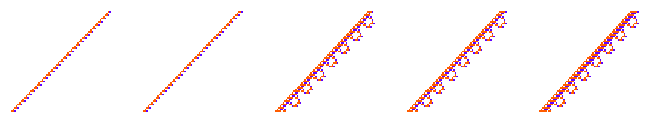
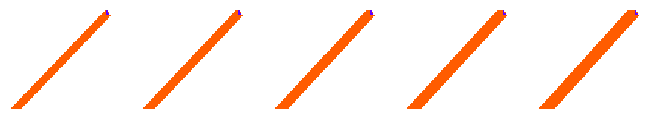
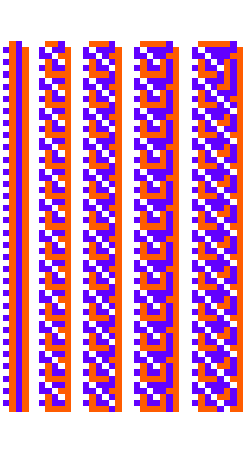
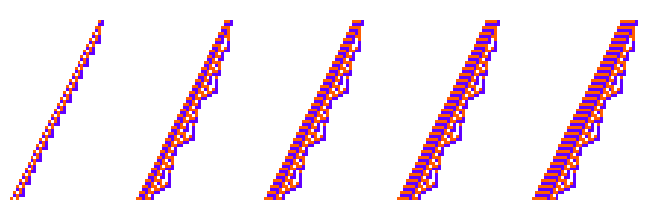
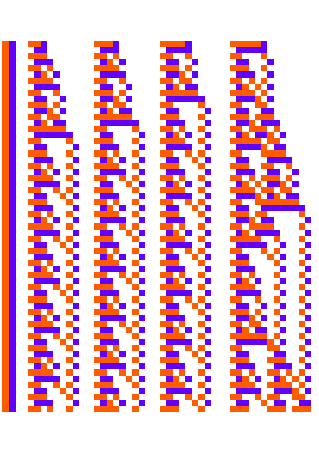
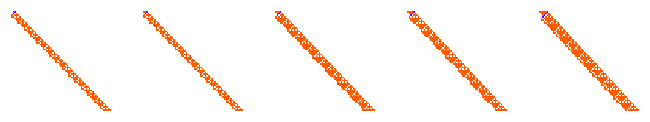
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 60], {i, 5}]]&/@[[All, -1]]
```

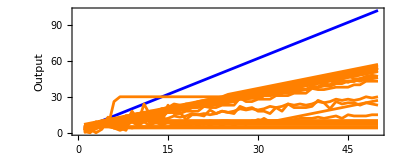

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Tooltip[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}], ArrayPlot[CellularAutomaton[#Rule,{Append[Table[1, 15], 2], 0},60]]]&/@ [[All, -1]]], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 60], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

```mathematica
ParallelTable[SeedRandom[221190 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>], {i , 100}]
```

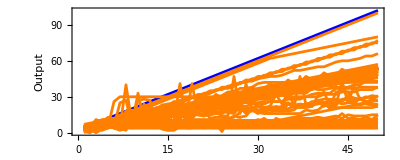

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Tooltip[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{60}}}], {i, 50}], ArrayPlot[CellularAutomaton[#Rule,{Append[Table[1, 15], 2], 0},60]]]&/@ [[All, -1]]], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 60], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Callout[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{100}}}], {i, 50}], #Rule]&/@ [[All, -1]]], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 60], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

-Graphics-

```mathematica
{5360672201868, 3, 1}
```

```mathematica
{4602200239314, 3, 1}
```

```mathematica
InputForm[{4602200239314,3,1}]
```

```mathematica
Position[[[All, -1]], {5360672201868, 3, 1}]
```

{{74,Key[Rule]}}

```mathematica
Position[[[All, -1]], {4602200239314, 3, 1}]
```

{{91,Key[Rule]}}

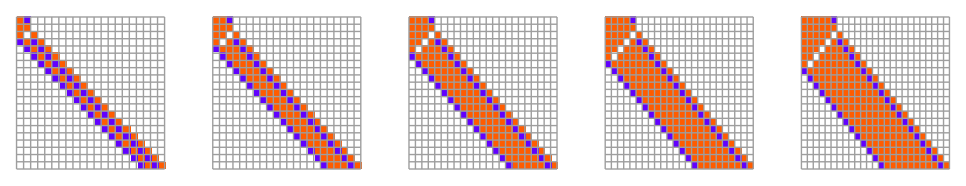

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]},Mesh->True]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 20], {i, 5}]]&@[[74, -1]]
```

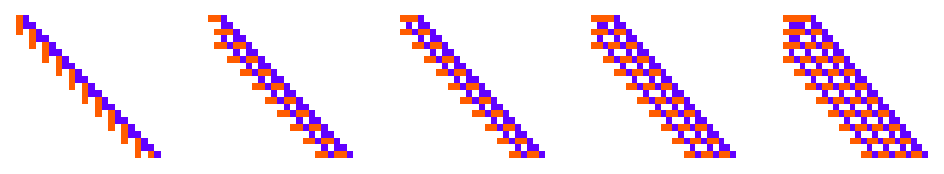

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 20], {i, 5}]]&@[[91, -1]]
```

```mathematica
ParallelTable[SeedRandom[221350 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i+2]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i+2]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>, "Final"], {i , 100}]
```

{<|Rule→{1040795051415,3,1},Fitness→-12|>,<|Rule→{3334966019541,3,1},Fitness→-14|>,<|Rule→{5071670737680,3,1},Fitness→-7|>,<|Rule→{6354123585966,3,1},Fitness→-12|>,<|Rule→{7041532331985,3,1},Fitness→-9|>,<|Rule→{6368544607824,3,1},Fitness→-5|>,<|Rule→{3778803208404,3,1},Fitness→-10|>,<|Rule→{3934850176542,3,1},Fitness→-7|>,<|Rule→{1797118471263,3,1},Fitness→-13|>,<|Rule→{6447408037026,3,1},Fitness→-14|>,<|Rule→{4414832095593,3,1},Fitness→-11|>,<|Rule→{1459367636706,3,1},Fitness→-6|>,<|Rule→{6183494901831,3,1},Fitness→-16|>,<|Rule→{5360672201868,3,1},Fitness→-10|>,<|Rule→{3564090178149,3,1},Fitness→-7|>,<|Rule→{2840660855649,3,1},Fitness→-10|>,<|Rule→{3508162040835,3,1},Fitness→-6|>,<|Rule→{5992031025540,3,1},Fitness→-12|>,<|Rule→{3029023762128,3,1},Fitness→-17|>,<|Rule→{4278355099203,3,1},Fitness→-13|>,<|Rule→{3531622153887,3,1},Fitness→-2|>,<|Rule→{4918245091632,3,1},Fitness→-14|>,<|Rule→{2981781669510,3,1},Fitness→-15|>,<|Rule→{2058959931195,3,1},Fitness→-7|>,<|Rule→{6829126495488,3,1},Fitness→-17|>,<|Rule→{7263564188712,3,1},Fitness→-20|>,<|Rule→{6831110435112,3,1},Fitness→0|>,<|Rule→{2322391097280,3,1},Fitness→-11|>,<|Rule→{3398866413813,3,1},Fitness→-5|>,<|Rule→{5568989845575,3,1},Fitness→-6|>,<|Rule→{4602200239314,3,1},Fitness→-16|>,<|Rule→{2724413964768,3,1},Fitness→-21|>,<|Rule→{934693775490,3,1},Fitness→-14|>,<|Rule→{4748052216675,3,1},Fitness→-13|>,<|Rule→{2849738728986,3,1},Fitness→-19|>,<|Rule→{3687350329494,3,1},Fitness→-20|>,<|Rule→{6073522368795,3,1},Fitness→-9|>,<|Rule→{801768250827,3,1},Fitness→-20|>,<|Rule→{4017449508732,3,1},Fitness→-10|>,<|Rule→{2829728481660,3,1},Fitness→-19|>,<|Rule→{5856197579274,3,1},Fitness→-7|>,<|Rule→{2373536404305,3,1},Fitness→-17|>,<|Rule→{4345532711919,3,1},Fitness→-16|>,<|Rule→{6092840520588,3,1},Fitness→-16|>,<|Rule→{6322135231722,3,1},Fitness→-6|>,<|Rule→{1529109170370,3,1},Fitness→-26|>,<|Rule→{5348682721224,3,1},Fitness→-20|>,<|Rule→{818594233023,3,1},Fitness→-14|>,<|Rule→{519614583723,3,1},Fitness→-4|>,<|Rule→{1227685177593,3,1},Fitness→-15|>,<|Rule→{5694513616974,3,1},Fitness→-7|>,<|Rule→{3055875630579,3,1},Fitness→-13|>,<|Rule→{3803545506474,3,1},Fitness→-6|>,<|Rule→{3167546970018,3,1},Fitness→-2|>,<|Rule→{4618763476596,3,1},Fitness→-15|>,<|Rule→{340087056366,3,1},Fitness→-13|>,<|Rule→{6918047769483,3,1},Fitness→-22|>,<|Rule→{4855395172605,3,1},Fitness→-7|>,<|Rule→{4742240849058,3,1},Fitness→-13|>,<|Rule→{2872133683674,3,1},Fitness→-10|>,<|Rule→{3666658155579,3,1},Fitness→-21|>,<|Rule→{4647192645294,3,1},Fitness→-2|>,<|Rule→{2219155979841,3,1},Fitness→-8|>,<|Rule→{3445701153540,3,1},Fitness→-8|>,<|Rule→{3737430230685,3,1},Fitness→-7|>,<|Rule→{5092396352703,3,1},Fitness→-20|>,<|Rule→{1224841831647,3,1},Fitness→-16|>,<|Rule→{6700889165373,3,1},Fitness→-15|>,<|Rule→{5319266756733,3,1},Fitness→-8|>,<|Rule→{2834940951540,3,1},Fitness→-25|>,<|Rule→{3206042286435,3,1},Fitness→-14|>,<|Rule→{3341972765490,3,1},Fitness→-7|>,<|Rule→{2721521184657,3,1},Fitness→-14|>,<|Rule→{6945985592646,3,1},Fitness→-21|>,<|Rule→{6233913361059,3,1},Fitness→-14|>,<|Rule→{1546005883671,3,1},Fitness→-20|>,<|Rule→{4084787111508,3,1},Fitness→-5|>,<|Rule→{1263820679379,3,1},Fitness→-4|>,<|Rule→{1079044307958,3,1},Fitness→-7|>,<|Rule→{2498449464318,3,1},Fitness→-12|>,<|Rule→{6228205074702,3,1},Fitness→-16|>,<|Rule→{5271044349501,3,1},Fitness→-24|>,<|Rule→{1487239249410,3,1},Fitness→-14|>,<|Rule→{6232641144699,3,1},Fitness→-6|>,<|Rule→{6806267643612,3,1},Fitness→-15|>,<|Rule→{6368228765472,3,1},Fitness→-11|>,<|Rule→{881318392065,3,1},Fitness→-17|>,<|Rule→{987366612339,3,1},Fitness→-13|>,<|Rule→{2219081700303,3,1},Fitness→-14|>,<|Rule→{4646157428070,3,1},Fitness→-12|>,<|Rule→{618355635129,3,1},Fitness→-19|>,<|Rule→{5431401145659,3,1},Fitness→-13|>,<|Rule→{1369887620805,3,1},Fitness→-4|>,<|Rule→{3071923850268,3,1},Fitness→-8|>,<|Rule→{1461601137312,3,1},Fitness→-7|>,<|Rule→{3361551039057,3,1},Fitness→-11|>,<|Rule→{3331126633404,3,1},Fitness→-6|>,<|Rule→{5435945324619,3,1},Fitness→-18|>,<|Rule→{1855626765192,3,1},Fitness→-4|>,<|Rule→{5436382333797,3,1},Fitness→-6|>}

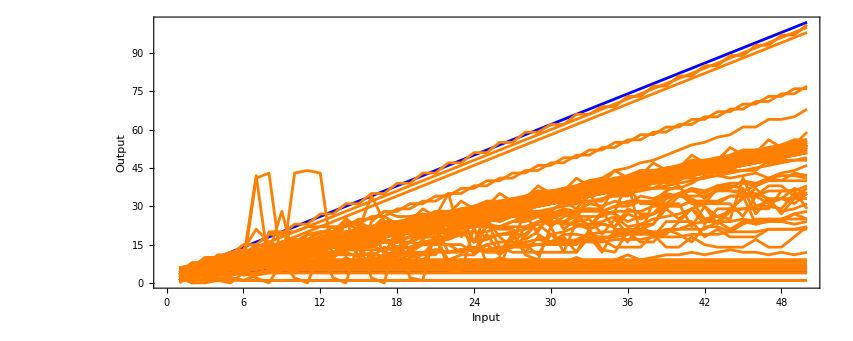

```mathematica
ListLinePlot[Join[{Table[ 2i+2, {i, 50}]}, Tooltip[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{100}}}], {i, 50}], ArrayPlot[CellularAutomaton[#Rule,{Append[Table[1, 15], 2], 0},60]]]&/@ ], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 60], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

```mathematica
ParallelTable[SeedRandom[221350 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i]&[#]] - CenterArray[Table[1, 2i+2], Max[Length[#],2i]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>, "Final"], {i , 200}]
```

{<|Rule→{3926879090433,3,1},Fitness→-1|>,<|Rule→{6554501783280,3,1},Fitness→-1|>,<|Rule→{1920624470631,3,1},Fitness→-7|>,<|Rule→{5675243520663,3,1},Fitness→-11|>,<|Rule→{6307299722943,3,1},Fitness→-12|>,<|Rule→{2829072854472,3,1},Fitness→-3|>,<|Rule→{2979634402068,3,1},Fitness→0|>,<|Rule→{4563634923549,3,1},Fitness→-6|>,<|Rule→{1165938587640,3,1},Fitness→-10|>,<|Rule→{2970292860153,3,1},Fitness→-3|>,<|Rule→{413800411809,3,1},Fitness→-2|>,<|Rule→{6385903144155,3,1},Fitness→-5|>,<|Rule→{6819444899082,3,1},Fitness→-3|>,<|Rule→{5348159699034,3,1},Fitness→-2|>,<|Rule→{710358817746,3,1},Fitness→-10|>,<|Rule→{7592462753463,3,1},Fitness→-3|>,<|Rule→{772293430134,3,1},Fitness→-1|>,<|Rule→{945495086877,3,1},Fitness→-6|>,<|Rule→{6093979512612,3,1},Fitness→-3|>,<|Rule→{3571744000227,3,1},Fitness→-9|>,<|Rule→{3030567474123,3,1},Fitness→-1|>,<|Rule→{2611441754784,3,1},Fitness→-12|>,<|Rule→{982682688753,3,1},Fitness→-1|>,<|Rule→{2355169967730,3,1},Fitness→-2|>,<|Rule→{5099306955384,3,1},Fitness→-1|>,<|Rule→{6746040026274,3,1},Fitness→-5|>,<|Rule→{1746178104924,3,1},Fitness→0|>,<|Rule→{4924769985015,3,1},Fitness→-9|>,<|Rule→{6735900017514,3,1},Fitness→-2|>,<|Rule→{2979596143719,3,1},Fitness→-2|>,<|Rule→{6750480819330,3,1},Fitness→-9|>,<|Rule→{1669650223026,3,1},Fitness→-1|>,<|Rule→{847431107493,3,1},Fitness→-9|>,<|Rule→{961250551668,3,1},Fitness→-7|>,<|Rule→{1158930698598,3,1},Fitness→-14|>,<|Rule→{4258949460714,3,1},Fitness→-1|>,<|Rule→{7620091116636,3,1},Fitness→-10|>,<|Rule→{6547579595064,3,1},Fitness→-12|>,<|Rule→{496728169470,3,1},Fitness→0|>,<|Rule→{2751597432525,3,1},Fitness→-7|>,<|Rule→{460526981148,3,1},Fitness→-9|>,<|Rule→{3841984630710,3,1},Fitness→-6|>,<|Rule→{955844716440,3,1},Fitness→-2|>,<|Rule→{4642242816060,3,1},Fitness→-10|>,<|Rule→{3989581924131,3,1},Fitness→-1|>,<|Rule→{3730325746362,3,1},Fitness→-2|>,<|Rule→{7586589952836,3,1},Fitness→-1|>,<|Rule→{2330800140459,3,1},Fitness→-3|>,<|Rule→{7622725290498,3,1},Fitness→-1|>,<|Rule→{1044925764459,3,1},Fitness→-17|>,<|Rule→{5705709810129,3,1},Fitness→-12|>,<|Rule→{3135859809879,3,1},Fitness→-2|>,<|Rule→{2637177300816,3,1},Fitness→-11|>,<|Rule→{3310715756865,3,1},Fitness→-1|>,<|Rule→{310038868566,3,1},Fitness→-12|>,<|Rule→{3093186832047,3,1},Fitness→-8|>,<|Rule→{2037588260934,3,1},Fitness→-9|>,<|Rule→{5546573670615,3,1},Fitness→-9|>,<|Rule→{6261568072689,3,1},Fitness→-2|>,<|Rule→{5096982206712,3,1},Fitness→-2|>,<|Rule→{1560007658538,3,1},Fitness→-16|>,<|Rule→{261578886327,3,1},Fitness→-11|>,<|Rule→{3105599734968,3,1},Fitness→-1|>,<|Rule→{955974877056,3,1},Fitness→-9|>,<|Rule→{2316910876029,3,1},Fitness→-1|>,<|Rule→{1638097595694,3,1},Fitness→-1|>,<|Rule→{2513476390293,3,1},Fitness→-8|>,<|Rule→{4034859163716,3,1},Fitness→-9|>,<|Rule→{1276418664009,3,1},Fitness→-8|>,<|Rule→{145748293881,3,1},Fitness→-2|>,<|Rule→{6546284876835,3,1},Fitness→-3|>,<|Rule→{3723104389248,3,1},Fitness→-11|>,<|Rule→{1643626262622,3,1},Fitness→-3|>,<|Rule→{7397217752643,3,1},Fitness→-6|>,<|Rule→{3757598306877,3,1},Fitness→-15|>,<|Rule→{6304821414165,3,1},Fitness→0|>,<|Rule→{6791554363860,3,1},Fitness→-10|>,<|Rule→{695273579817,3,1},Fitness→-3|>,<|Rule→{364114004958,3,1},Fitness→-8|>,<|Rule→{4147440740835,3,1},Fitness→0|>,<|Rule→{3942992787822,3,1},Fitness→-6|>,<|Rule→{6241412883756,3,1},Fitness→-1|>,<|Rule→{5111694737832,3,1},Fitness→-1|>,<|Rule→{5598171779859,3,1},Fitness→-2|>,<|Rule→{1143974828985,3,1},Fitness→-5|>,<|Rule→{3066760862991,3,1},Fitness→-3|>,<|Rule→{423238329618,3,1},Fitness→-3|>,<|Rule→{5944085614620,3,1},Fitness→-14|>,<|Rule→{2538888414786,3,1},Fitness→-1|>,<|Rule→{6493968513774,3,1},Fitness→0|>,<|Rule→{6378805713528,3,1},Fitness→-10|>,<|Rule→{6639477784749,3,1},Fitness→-11|>,<|Rule→{890351338998,3,1},Fitness→-3|>,<|Rule→{3989938315212,3,1},Fitness→-10|>,<|Rule→{1149891732690,3,1},Fitness→-3|>,<|Rule→{3757175146386,3,1},Fitness→-8|>,<|Rule→{2494656399078,3,1},Fitness→-9|>,<|Rule→{101530623177,3,1},Fitness→-1|>,<|Rule→{1956681145848,3,1},Fitness→-2|>,<|Rule→{2686739544972,3,1},Fitness→-6|>,<|Rule→{859269285306,3,1},Fitness→-14|>,<|Rule→{1926184597365,3,1},Fitness→-3|>,<|Rule→{2934273661782,3,1},Fitness→-2|>,<|Rule→{4684180545342,3,1},Fitness→-10|>,<|Rule→{807319653225,3,1},Fitness→-6|>,<|Rule→{2826079970316,3,1},Fitness→-9|>,<|Rule→{3508894595580,3,1},Fitness→-2|>,<|Rule→{5989678627590,3,1},Fitness→-14|>,<|Rule→{3590686441098,3,1},Fitness→-4|>,<|Rule→{3025784103678,3,1},Fitness→-8|>,<|Rule→{5292314227578,3,1},Fitness→-3|>,<|Rule→{2119397752722,3,1},Fitness→-2|>,<|Rule→{2410540741866,3,1},Fitness→-10|>,<|Rule→{7234510237860,3,1},Fitness→-2|>,<|Rule→{6803096161374,3,1},Fitness→-14|>,<|Rule→{5642131305195,3,1},Fitness→0|>,<|Rule→{5642375180481,3,1},Fitness→0|>,<|Rule→{3187399622931,3,1},Fitness→-9|>,<|Rule→{673544442315,3,1},Fitness→-1|>,<|Rule→{3258126309873,3,1},Fitness→-9|>,<|Rule→{7135589104851,3,1},Fitness→-2|>,<|Rule→{602300964762,3,1},Fitness→-14|>,<|Rule→{2544522314625,3,1},Fitness→-12|>,<|Rule→{3829512917844,3,1},Fitness→-12|>,<|Rule→{6349900062588,3,1},Fitness→-2|>,<|Rule→{2794311796149,3,1},Fitness→-11|>,<|Rule→{5841040167501,3,1},Fitness→-4|>,<|Rule→{3452173635708,3,1},Fitness→-12|>,<|Rule→{3400054616475,3,1},Fitness→-2|>,<|Rule→{726600369234,3,1},Fitness→-9|>,<|Rule→{3738783047481,3,1},Fitness→-12|>,<|Rule→{4480721839017,3,1},Fitness→-16|>,<|Rule→{3940585739739,3,1},Fitness→-8|>,<|Rule→{6394310422839,3,1},Fitness→-8|>,<|Rule→{4718214167646,3,1},Fitness→-2|>,<|Rule→{6612633639981,3,1},Fitness→-3|>,<|Rule→{4194169016949,3,1},Fitness→-2|>,<|Rule→{2939140622304,3,1},Fitness→-10|>,<|Rule→{3781394694180,3,1},Fitness→-6|>,<|Rule→{4478388185478,3,1},Fitness→-3|>,<|Rule→{4090718057193,3,1},Fitness→-7|>,<|Rule→{1834644175857,3,1},Fitness→-6|>,<|Rule→{1479744800340,3,1},Fitness→-6|>,<|Rule→{5172453096921,3,1},Fitness→-13|>,<|Rule→{4726479304290,3,1},Fitness→-2|>,<|Rule→{6417102602778,3,1},Fitness→-3|>,<|Rule→{165217320357,3,1},Fitness→-7|>,<|Rule→{3405585835914,3,1},Fitness→-3|>,<|Rule→{2612039334180,3,1},Fitness→-6|>,<|Rule→{3618528581526,3,1},Fitness→-3|>,<|Rule→{3687222831480,3,1},Fitness→-8|>,<|Rule→{2493089586438,3,1},Fitness→-7|>,<|Rule→{7450691053764,3,1},Fitness→-2|>,<|Rule→{1436744808792,3,1},Fitness→-15|>,<|Rule→{6359058638694,3,1},Fitness→-11|>,<|Rule→{5500282694571,3,1},Fitness→-2|>,<|Rule→{3868648681017,3,1},Fitness→-5|>,<|Rule→{6645831331242,3,1},Fitness→-8|>,<|Rule→{3530512320339,3,1},Fitness→-2|>,<|Rule→{2442339389466,3,1},Fitness→0|>,<|Rule→{3077929239492,3,1},Fitness→-13|>,<|Rule→{1203535307010,3,1},Fitness→-2|>,<|Rule→{2930656552380,3,1},Fitness→-6|>,<|Rule→{3853607205876,3,1},Fitness→-8|>,<|Rule→{3725463027267,3,1},Fitness→-10|>,<|Rule→{5002839311934,3,1},Fitness→-1|>,<|Rule→{2914534289799,3,1},Fitness→-3|>,<|Rule→{2666866315626,3,1},Fitness→-3|>,<|Rule→{153426212694,3,1},Fitness→-13|>,<|Rule→{1236158701755,3,1},Fitness→-7|>,<|Rule→{357567462780,3,1},Fitness→-6|>,<|Rule→{7181036663139,3,1},Fitness→-13|>,<|Rule→{3239806653975,3,1},Fitness→-5|>,<|Rule→{2857034165265,3,1},Fitness→-9|>,<|Rule→{5605148743755,3,1},Fitness→-2|>,<|Rule→{3996560625576,3,1},Fitness→-2|>,<|Rule→{4462136783454,3,1},Fitness→-10|>,<|Rule→{3800918634075,3,1},Fitness→-11|>,<|Rule→{968338748757,3,1},Fitness→-10|>,<|Rule→{2967148079775,3,1},Fitness→-10|>,<|Rule→{1307766702444,3,1},Fitness→-9|>,<|Rule→{5760834811911,3,1},Fitness→-8|>,<|Rule→{3785668668342,3,1},Fitness→-14|>,<|Rule→{4293744323691,3,1},Fitness→-8|>,<|Rule→{5631881119086,3,1},Fitness→-2|>,<|Rule→{200117192955,3,1},Fitness→-8|>,<|Rule→{3191122930194,3,1},Fitness→0|>,<|Rule→{4407624336237,3,1},Fitness→-1|>,<|Rule→{786317691969,3,1},Fitness→0|>,<|Rule→{6174501282684,3,1},Fitness→-4|>,<|Rule→{6091471578009,3,1},Fitness→-5|>,<|Rule→{3886790893149,3,1},Fitness→-5|>,<|Rule→{4193877234771,3,1},Fitness→-1|>,<|Rule→{3868798576041,3,1},Fitness→-13|>,<|Rule→{2714608498482,3,1},Fitness→-9|>,<|Rule→{36166577667,3,1},Fitness→-9|>,<|Rule→{4101707668635,3,1},Fitness→-10|>,<|Rule→{7507244759682,3,1},Fitness→-8|>,<|Rule→{4267334014353,3,1},Fitness→-1|>,<|Rule→{3086399054865,3,1},Fitness→-2|>}

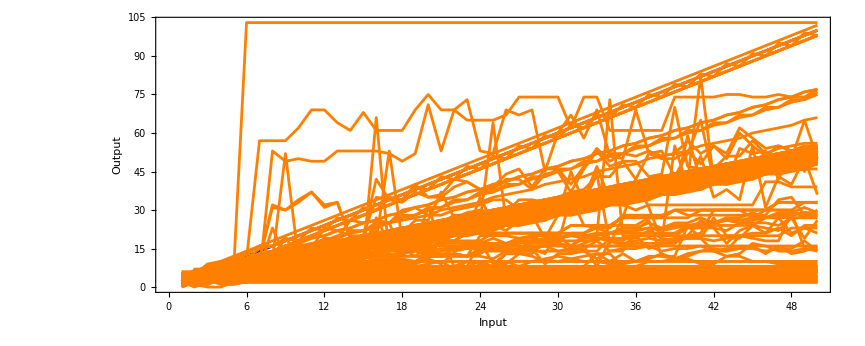

```mathematica
ListLinePlot[Join[{Table[ 2i, {i, 50}]}, Tooltip[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}], ArrayPlot[CellularAutomaton[#Rule,{Append[Table[1, 15], 2], 0},60]]]&/@ ], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 200], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

```mathematica
Select[Differences[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]]&/@, AllTrue[#, # ==2&]&->"Index"]
```

{160,169}

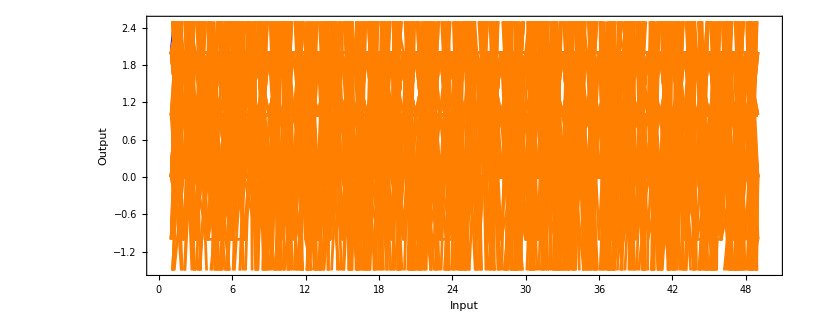

```mathematica
ListLinePlot[Join[{Table[ 2i, {i, 50}]}, Tooltip[Differences[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]], ArrayPlot[CellularAutomaton[#Rule,{Append[Table[1, 15], 2], 0},60]]]&/@ ], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 200], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

```mathematica
TakeSmallestBy[runs, Abs[(Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]) - Table[ 2i, {i, 50}]]&, 5]
```

{<|Rule→{6174501282684,3,1},Fitness→-4|>,<|Rule→{1920624470631,3,1},Fitness→-7|>,<|Rule→{3093186832047,3,1},Fitness→-8|>,<|Rule→{2513476390293,3,1},Fitness→-8|>,<|Rule→{3942992787822,3,1},Fitness→-6|>}

```mathematica
ListLinePlot[Join[{Table[ 2i, {i, 50}]}, Callout[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}], #Rule]&/@ runs], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 200], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4]
```

```mathematica
runs = ;
```

```mathematica
Select[, #Fitness== 0&->"Index"]
```

{7,27,39,76,80,90,116,117,160,187,189}

```mathematica
[[]]
```

Part::partd: Part specification Null⟦{7,27,39,76,80,90,116,117,160,187,189}⟧ is longer than depth of object.

Null⟦{7,27,39,76,80,90,116,117,160,187,189}⟧

```mathematica
runs[[]]
```

{<|Rule→{2979634402068,3,1},Fitness→0|>,<|Rule→{1746178104924,3,1},Fitness→0|>,<|Rule→{496728169470,3,1},Fitness→0|>,<|Rule→{6304821414165,3,1},Fitness→0|>,<|Rule→{4147440740835,3,1},Fitness→0|>,<|Rule→{6493968513774,3,1},Fitness→0|>,<|Rule→{5642131305195,3,1},Fitness→0|>,<|Rule→{5642375180481,3,1},Fitness→0|>,<|Rule→{2442339389466,3,1},Fitness→0|>,<|Rule→{3191122930194,3,1},Fitness→0|>,<|Rule→{786317691969,3,1},Fitness→0|>}

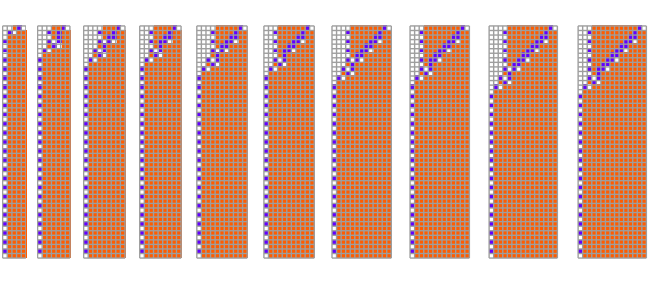
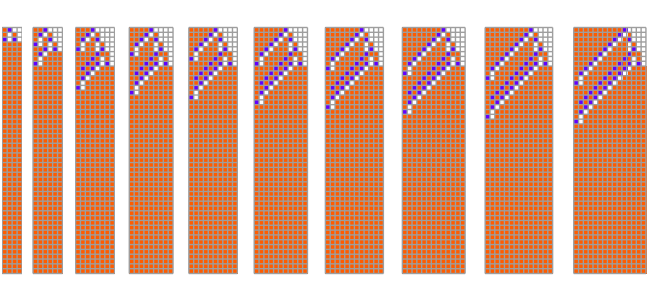
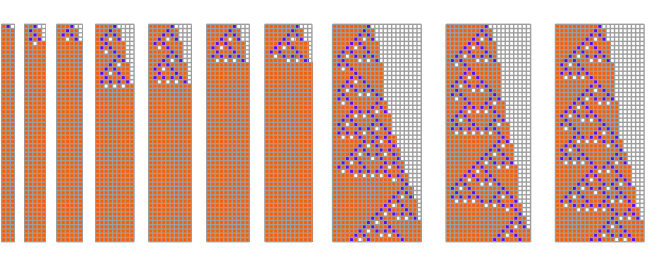
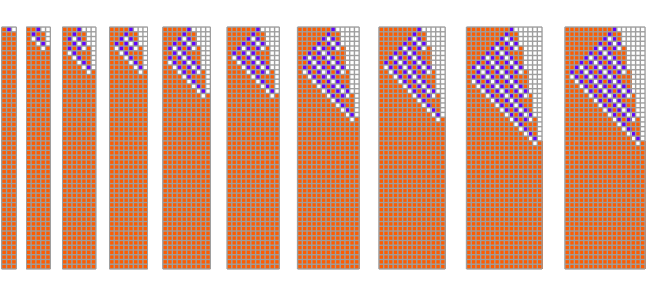
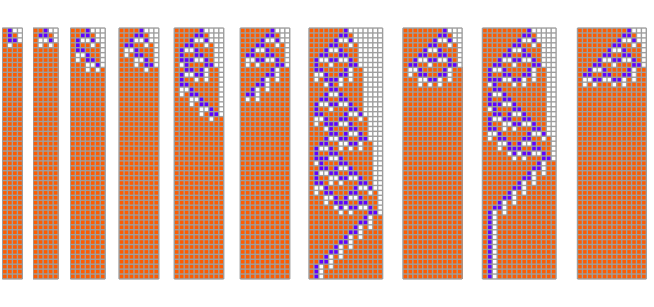
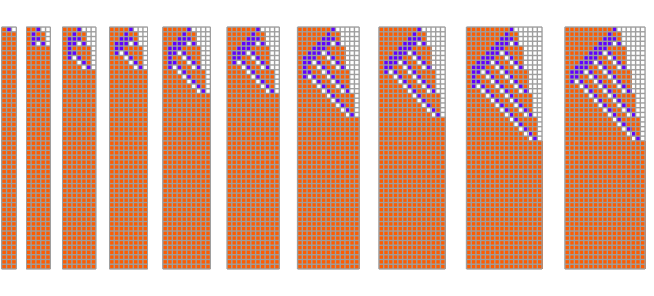
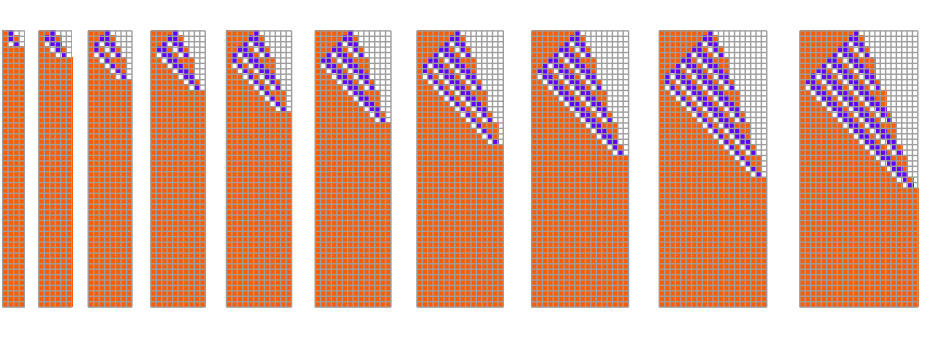
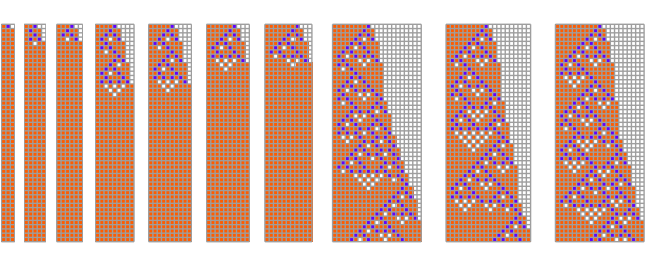
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]},Mesh->True]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 50], {i, 10}]]&/@runs[[]]
```

```mathematica
ParallelTable[SeedRandom[221350 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i]&[#]] - CenterArray[Table[1, 2i], Max[Length[#],2i]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>, "Final"], {i , 200}]
```

{<|Rule→{3900969747819,3,1},Fitness→-3|>,<|Rule→{6551053255809,3,1},Fitness→-4|>,<|Rule→{1920624470631,3,1},Fitness→-11|>,<|Rule→{5345175320154,3,1},Fitness→-13|>,<|Rule→{2200394492271,3,1},Fitness→-12|>,<|Rule→{3018693361992,3,1},Fitness→-4|>,<|Rule→{6343841464197,3,1},Fitness→-7|>,<|Rule→{322427002149,3,1},Fitness→-5|>,<|Rule→{1646029279944,3,1},Fitness→-10|>,<|Rule→{1335876775011,3,1},Fitness→-6|>,<|Rule→{6323455324365,3,1},Fitness→-4|>,<|Rule→{2870325217530,3,1},Fitness→-10|>,<|Rule→{5681581291611,3,1},Fitness→-4|>,<|Rule→{5294638339590,3,1},Fitness→-5|>,<|Rule→{634772576325,3,1},Fitness→-11|>,<|Rule→{6741874793268,3,1},Fitness→-4|>,<|Rule→{4700437755462,3,1},Fitness→-3|>,<|Rule→{1029024616437,3,1},Fitness→-4|>,<|Rule→{4490482958211,3,1},Fitness→-5|>,<|Rule→{7558324160283,3,1},Fitness→-14|>,<|Rule→{3760215822180,3,1},Fitness→-6|>,<|Rule→{1052888042799,3,1},Fitness→-9|>,<|Rule→{2810672730198,3,1},Fitness→-9|>,<|Rule→{1055914398684,3,1},Fitness→-6|>,<|Rule→{5085302542437,3,1},Fitness→-5|>,<|Rule→{6715051229361,3,1},Fitness→-5|>,<|Rule→{20253478293,3,1},Fitness→-10|>,<|Rule→{4077481375572,3,1},Fitness→-10|>,<|Rule→{6411701109972,3,1},Fitness→-5|>,<|Rule→{2153060715501,3,1},Fitness→-4|>,<|Rule→{6767010580131,3,1},Fitness→-9|>,<|Rule→{1149884797908,3,1},Fitness→-5|>,<|Rule→{3500844863559,3,1},Fitness→-4|>,<|Rule→{364959399006,3,1},Fitness→-15|>,<|Rule→{3753276800256,3,1},Fitness→-5|>,<|Rule→{3718502421279,3,1},Fitness→0|>,<|Rule→{2926006913127,3,1},Fitness→-4|>,<|Rule→{6620424272685,3,1},Fitness→-13|>,<|Rule→{4666013557461,3,1},Fitness→-4|>,<|Rule→{555696396516,3,1},Fitness→-10|>,<|Rule→{3999588823863,3,1},Fitness→-11|>,<|Rule→{2236898655540,3,1},Fitness→-12|>,<|Rule→{37600700838,3,1},Fitness→-4|>,<|Rule→{3805542464301,3,1},Fitness→-9|>,<|Rule→{4647115863234,3,1},Fitness→-4|>,<|Rule→{707576913729,3,1},Fitness→-8|>,<|Rule→{7304289502842,3,1},Fitness→-4|>,<|Rule→{1985397802815,3,1},Fitness→-8|>,<|Rule→{2678548290210,3,1},Fitness→-12|>,<|Rule→{1037048214516,3,1},Fitness→-18|>,<|Rule→{3242997149166,3,1},Fitness→-17|>,<|Rule→{3796108325910,3,1},Fitness→-2|>,<|Rule→{5748590818125,3,1},Fitness→-17|>,<|Rule→{600321787386,3,1},Fitness→-4|>,<|Rule→{413825579874,3,1},Fitness→-15|>,<|Rule→{3249734930487,3,1},Fitness→-12|>,<|Rule→{1448819124462,3,1},Fitness→-17|>,<|Rule→{3995289719349,3,1},Fitness→-4|>,<|Rule→{6239427829734,3,1},Fitness→-5|>,<|Rule→{5096924994306,3,1},Fitness→-5|>,<|Rule→{1560007658538,3,1},Fitness→-16|>,<|Rule→{7178060503197,3,1},Fitness→-13|>,<|Rule→{2987049118794,3,1},Fitness→-3|>,<|Rule→{3497974153857,3,1},Fitness→-8|>,<|Rule→{6730189671348,3,1},Fitness→-4|>,<|Rule→{2314672290918,3,1},Fitness→-5|>,<|Rule→{1608103357020,3,1},Fitness→-9|>,<|Rule→{6006714841767,3,1},Fitness→-12|>,<|Rule→{2688522984822,3,1},Fitness→-9|>,<|Rule→{62052084909,3,1},Fitness→-10|>,<|Rule→{3182943875139,3,1},Fitness→-5|>,<|Rule→{3622316796270,3,1},Fitness→-6|>,<|Rule→{1089096518955,3,1},Fitness→-9|>,<|Rule→{405105492591,3,1},Fitness→-4|>,<|Rule→{7610502141534,3,1},Fitness→-15|>,<|Rule→{1189560484692,3,1},Fitness→-4|>,<|Rule→{6896022791211,3,1},Fitness→-13|>,<|Rule→{7224092813703,3,1},Fitness→-2|>,<|Rule→{1211531810688,3,1},Fitness→-12|>,<|Rule→{1461373238472,3,1},Fitness→-10|>,<|Rule→{1782250462632,3,1},Fitness→-22|>,<|Rule→{5498676842691,3,1},Fitness→-8|>,<|Rule→{6793826558223,3,1},Fitness→-5|>,<|Rule→{6193726054434,3,1},Fitness→-13|>,<|Rule→{448818114525,3,1},Fitness→-7|>,<|Rule→{2133363148524,3,1},Fitness→-11|>,<|Rule→{1519742587785,3,1},Fitness→-4|>,<|Rule→{6352517083725,3,1},Fitness→-4|>,<|Rule→{2255248608300,3,1},Fitness→-3|>,<|Rule→{7555452960060,3,1},Fitness→-6|>,<|Rule→{6378805713528,3,1},Fitness→-11|>,<|Rule→{3984614774820,3,1},Fitness→-11|>,<|Rule→{2858014472286,3,1},Fitness→-4|>,<|Rule→{5979470603427,3,1},Fitness→-11|>,<|Rule→{3906766538235,3,1},Fitness→-9|>,<|Rule→{3746628477393,3,1},Fitness→-9|>,<|Rule→{1647367973343,3,1},Fitness→-9|>,<|Rule→{2349468658035,3,1},Fitness→-6|>,<|Rule→{1893861699042,3,1},Fitness→-5|>,<|Rule→{697795044111,3,1},Fitness→-15|>,<|Rule→{4084406449020,3,1},Fitness→-16|>,<|Rule→{1811033076846,3,1},Fitness→-9|>,<|Rule→{3687165766518,3,1},Fitness→-6|>,<|Rule→{2152693764126,3,1},Fitness→-13|>,<|Rule→{5393574810297,3,1},Fitness→-4|>,<|Rule→{4945531967178,3,1},Fitness→-8|>,<|Rule→{3633256572549,3,1},Fitness→-2|>,<|Rule→{6940464419493,3,1},Fitness→-15|>,<|Rule→{488701822941,3,1},Fitness→-4|>,<|Rule→{3152515237281,3,1},Fitness→-9|>,<|Rule→{5281911210657,3,1},Fitness→-5|>,<|Rule→{1251130693728,3,1},Fitness→-5|>,<|Rule→{647656170960,3,1},Fitness→-9|>,<|Rule→{5749010823837,3,1},Fitness→-4|>,<|Rule→{6792635808171,3,1},Fitness→-14|>,<|Rule→{6996319217613,3,1},Fitness→-6|>,<|Rule→{889825869657,3,1},Fitness→-4|>,<|Rule→{4815803630943,3,1},Fitness→-9|>,<|Rule→{7173885990882,3,1},Fitness→-5|>,<|Rule→{4802599669980,3,1},Fitness→-10|>,<|Rule→{5377861988724,3,1},Fitness→-2|>,<|Rule→{602300964762,3,1},Fitness→-15|>,<|Rule→{3444519937131,3,1},Fitness→-5|>,<|Rule→{5435674879437,3,1},Fitness→-11|>,<|Rule→{5137253147865,3,1},Fitness→-10|>,<|Rule→{7508315149074,3,1},Fitness→-13|>,<|Rule→{7255596989868,3,1},Fitness→-7|>,<|Rule→{3452173635708,3,1},Fitness→-12|>,<|Rule→{5733920928402,3,1},Fitness→-15|>,<|Rule→{109396491555,3,1},Fitness→-10|>,<|Rule→{4120305761835,3,1},Fitness→-20|>,<|Rule→{2977233237909,3,1},Fitness→-4|>,<|Rule→{3616248873966,3,1},Fitness→-4|>,<|Rule→{3106527575112,3,1},Fitness→-12|>,<|Rule→{2486829870696,3,1},Fitness→-5|>,<|Rule→{6612633639981,3,1},Fitness→-5|>,<|Rule→{1756423281600,3,1},Fitness→-6|>,<|Rule→{6107528937915,3,1},Fitness→-10|>,<|Rule→{172638622053,3,1},Fitness→-6|>,<|Rule→{6494886312807,3,1},Fitness→-3|>,<|Rule→{3797751579759,3,1},Fitness→-8|>,<|Rule→{404976351681,3,1},Fitness→-4|>,<|Rule→{2894296540065,3,1},Fitness→-12|>,<|Rule→{6244120408725,3,1},Fitness→-10|>,<|Rule→{3053669139462,3,1},Fitness→-5|>,<|Rule→{3017950110285,3,1},Fitness→-6|>,<|Rule→{106998687321,3,1},Fitness→-8|>,<|Rule→{5407377817845,3,1},Fitness→-5|>,<|Rule→{2583001988370,3,1},Fitness→-8|>,<|Rule→{2571459897387,3,1},Fitness→-5|>,<|Rule→{6453628851636,3,1},Fitness→-6|>,<|Rule→{4635252085848,3,1},Fitness→-10|>,<|Rule→{7458898628811,3,1},Fitness→-5|>,<|Rule→{3989333325357,3,1},Fitness→-6|>,<|Rule→{6368351720499,3,1},Fitness→-12|>,<|Rule→{4748180136129,3,1},Fitness→-3|>,<|Rule→{4805383652778,3,1},Fitness→-4|>,<|Rule→{1536782585619,3,1},Fitness→-10|>,<|Rule→{4344609840828,3,1},Fitness→-6|>,<|Rule→{4778313271524,3,1},Fitness→-7|>,<|Rule→{4915552715310,3,1},Fitness→-13|>,<|Rule→{4391210662554,3,1},Fitness→-9|>,<|Rule→{3871164775662,3,1},Fitness→-15|>,<|Rule→{4149965106639,3,1},Fitness→-15|>,<|Rule→{6478735311504,3,1},Fitness→-5|>,<|Rule→{4992321503091,3,1},Fitness→-5|>,<|Rule→{1200753448086,3,1},Fitness→-7|>,<|Rule→{684810335553,3,1},Fitness→-8|>,<|Rule→{144519618762,3,1},Fitness→-15|>,<|Rule→{3938300818452,3,1},Fitness→-6|>,<|Rule→{2608007011161,3,1},Fitness→-13|>,<|Rule→{7223514280101,3,1},Fitness→-15|>,<|Rule→{5987385378387,3,1},Fitness→-4|>,<|Rule→{1176277832451,3,1},Fitness→-6|>,<|Rule→{7540127490954,3,1},Fitness→-5|>,<|Rule→{6018713527896,3,1},Fitness→-4|>,<|Rule→{597997440384,3,1},Fitness→-4|>,<|Rule→{4707482578605,3,1},Fitness→-10|>,<|Rule→{2839835595249,3,1},Fitness→-10|>,<|Rule→{3432080811618,3,1},Fitness→-10|>,<|Rule→{944925782253,3,1},Fitness→-12|>,<|Rule→{4089576397041,3,1},Fitness→-6|>,<|Rule→{6322885448616,3,1},Fitness→-15|>,<|Rule→{4294017314763,3,1},Fitness→-5|>,<|Rule→{3812656943826,3,1},Fitness→-4|>,<|Rule→{3530341660080,3,1},Fitness→-7|>,<|Rule→{3191122930194,3,1},Fitness→-3|>,<|Rule→{5678004630891,3,1},Fitness→-6|>,<|Rule→{650141632980,3,1},Fitness→-9|>,<|Rule→{1852178268015,3,1},Fitness→-9|>,<|Rule→{6039518968947,3,1},Fitness→-5|>,<|Rule→{3016606211319,3,1},Fitness→-5|>,<|Rule→{3713977675494,3,1},Fitness→-3|>,<|Rule→{3269125257849,3,1},Fitness→-11|>,<|Rule→{2818589175126,3,1},Fitness→-3|>,<|Rule→{1919073203385,3,1},Fitness→-15|>,<|Rule→{6614645450940,3,1},Fitness→-16|>,<|Rule→{5669016081834,3,1},Fitness→-5|>,<|Rule→{6167526220278,3,1},Fitness→-4|>,<|Rule→{3033910753302,3,1},Fitness→-5|>}

```mathematica
Select[, #Fitness== 0&->"Index"]
```

{36}

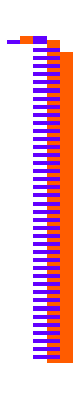
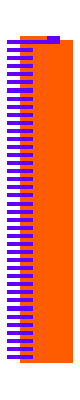
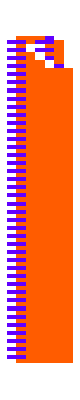
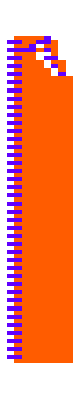
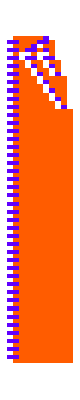
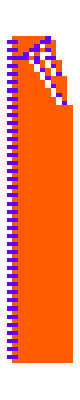
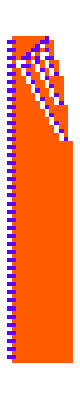
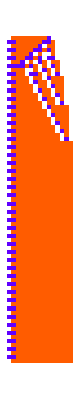

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 80], {i, 20}]]&/@[[Select[, #Fitness== 0&->"Index"]]]
```

```mathematica
ListLinePlot[Join[{Table[ 2i, {i, 50}]}, Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]]&/@ [[Select[, #Fitness== 0&->"Index"]]]]
```

-Graphics-

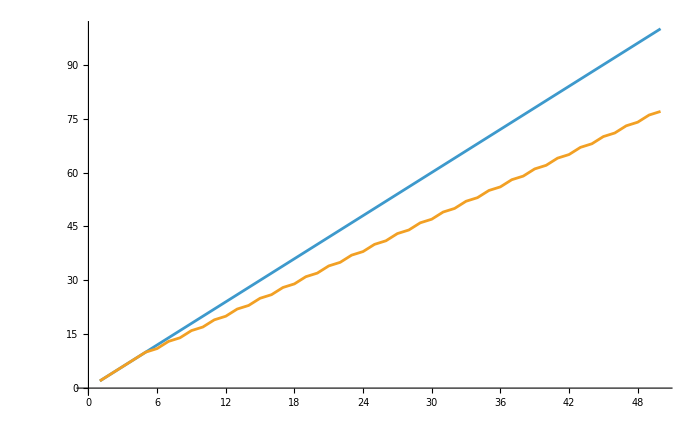

```mathematica
ListLinePlot[Join[{Table[ 2i, {i, 50}]}, Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]&/@ [[Select[, #Fitness== 0&->"Index"]]]]]
```

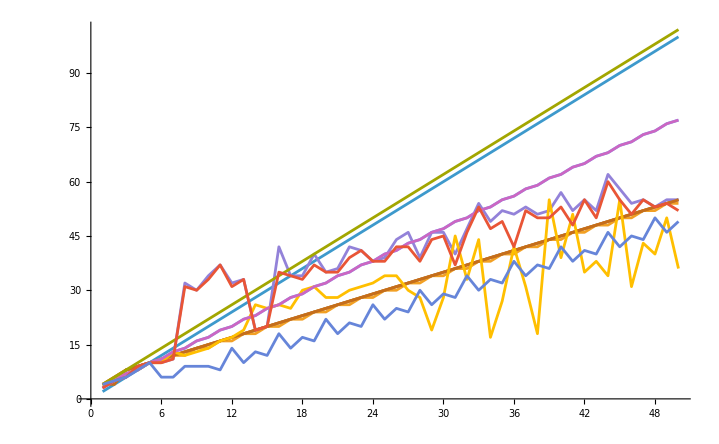

```mathematica
ListLinePlot[Tooltip[Join[{Table[ 2i, {i, 50}]}, Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]&/@ runs[[]]], ]
```

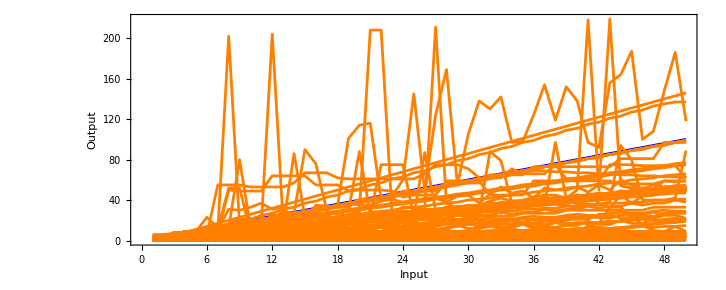

```mathematica
ListLinePlot[Join[{Table[ 2i, {i, 50}]}, Tooltip[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}], ArrayPlot[CellularAutomaton[#Rule,{Append[Table[1, 15], 2], 0},200]]]&/@ ], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 200], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4, PlotRange->All]
```

```mathematica
ParallelTable[SeedRandom[221350 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i]&[#]] - CenterArray[Table[1, 2i], Max[Length[#],2i]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>, "Final"], {i , 200}]
```

```mathematica
ParallelTable[SeedRandom[221350 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[2i - Count[#, 1]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]]]&)|>, "Final"], {i , 200}]
```

{<|Rule→{4019820974163,3,1},Fitness→-5|>,<|Rule→{4007514803679,3,1},Fitness→-3|>,<|Rule→{7097049833943,3,1},Fitness→0|>,<|Rule→{1933779937377,3,1},Fitness→-3|>,<|Rule→{6262239456594,3,1},Fitness→-8|>,<|Rule→{2832951536760,3,1},Fitness→-2|>,<|Rule→{4970276989125,3,1},Fitness→-2|>,<|Rule→{6448936441437,3,1},Fitness→-2|>,<|Rule→{5102087061960,3,1},Fitness→-4|>,<|Rule→{6323332765041,3,1},Fitness→0|>,<|Rule→{4429829714646,3,1},Fitness→-4|>,<|Rule→{2430896849307,3,1},Fitness→-3|>,<|Rule→{4164980620941,3,1},Fitness→-4|>,<|Rule→{5523384175257,3,1},Fitness→-2|>,<|Rule→{174613146312,3,1},Fitness→-5|>,<|Rule→{2956118150880,3,1},Fitness→-5|>,<|Rule→{1682123971635,3,1},Fitness→-4|>,<|Rule→{464160639960,3,1},Fitness→-3|>,<|Rule→{2758339881552,3,1},Fitness→-2|>,<|Rule→{2756459261439,3,1},Fitness→-2|>,<|Rule→{4594716666657,3,1},Fitness→-4|>,<|Rule→{726072833520,3,1},Fitness→-6|>,<|Rule→{3458310352125,3,1},Fitness→0|>,<|Rule→{5650493886054,3,1},Fitness→-6|>,<|Rule→{4276561891629,3,1},Fitness→0|>,<|Rule→{2388881346603,3,1},Fitness→-6|>,<|Rule→{2438157855825,3,1},Fitness→-8|>,<|Rule→{3475516566996,3,1},Fitness→-8|>,<|Rule→{7600575711162,3,1},Fitness→-4|>,<|Rule→{1416819657153,3,1},Fitness→-4|>,<|Rule→{7024282169958,3,1},Fitness→-3|>,<|Rule→{5970699358779,3,1},Fitness→-4|>,<|Rule→{4264993540941,3,1},Fitness→-3|>,<|Rule→{139747926960,3,1},Fitness→-3|>,<|Rule→{2639535809052,3,1},Fitness→-4|>,<|Rule→{7030004314893,3,1},Fitness→-4|>,<|Rule→{3394007752062,3,1},Fitness→-2|>,<|Rule→{2782096402374,3,1},Fitness→-5|>,<|Rule→{4215845285088,3,1},Fitness→-4|>,<|Rule→{371202691944,3,1},Fitness→-1|>,<|Rule→{3046597784370,3,1},Fitness→-3|>,<|Rule→{1306314229776,3,1},Fitness→-5|>,<|Rule→{2167932258642,3,1},Fitness→-5|>,<|Rule→{3090725759274,3,1},Fitness→-2|>,<|Rule→{1293918487857,3,1},Fitness→-3|>,<|Rule→{7077218547402,3,1},Fitness→-10|>,<|Rule→{2047445795355,3,1},Fitness→-1|>,<|Rule→{4096192113690,3,1},Fitness→-2|>,<|Rule→{5999482359702,3,1},Fitness→0|>,<|Rule→{3281159866878,3,1},Fitness→-9|>,<|Rule→{2323671178305,3,1},Fitness→-3|>,<|Rule→{453427364901,3,1},Fitness→0|>,<|Rule→{238012673793,3,1},Fitness→0|>,<|Rule→{3194014631421,3,1},Fitness→-3|>,<|Rule→{6425947950885,3,1},Fitness→-4|>,<|Rule→{5439347795277,3,1},Fitness→-3|>,<|Rule→{3434339162295,3,1},Fitness→-5|>,<|Rule→{521897335890,3,1},Fitness→-4|>,<|Rule→{7447277248527,3,1},Fitness→-2|>,<|Rule→{774694375644,3,1},Fitness→-2|>,<|Rule→{821794851000,3,1},Fitness→-4|>,<|Rule→{2257949952108,3,1},Fitness→-2|>,<|Rule→{2328697058541,3,1},Fitness→-4|>,<|Rule→{5530848304482,3,1},Fitness→-6|>,<|Rule→{3923292122442,3,1},Fitness→-1|>,<|Rule→{7599919798707,3,1},Fitness→-4|>,<|Rule→{4209425020050,3,1},Fitness→-5|>,<|Rule→{7032448570566,3,1},Fitness→-2|>,<|Rule→{697526397165,3,1},Fitness→-3|>,<|Rule→{1743656792952,3,1},Fitness→-4|>,<|Rule→{6446080004886,3,1},Fitness→-6|>,<|Rule→{4000870204611,3,1},Fitness→-2|>,<|Rule→{5025721731384,3,1},Fitness→-1|>,<|Rule→{4219125791031,3,1},Fitness→-6|>,<|Rule→{7331957331276,3,1},Fitness→-3|>,<|Rule→{1528496371185,3,1},Fitness→-5|>,<|Rule→{3936092991030,3,1},Fitness→-4|>,<|Rule→{5289540798894,3,1},Fitness→-4|>,<|Rule→{1850690821023,3,1},Fitness→-2|>,<|Rule→{5294850501525,3,1},Fitness→-4|>,<|Rule→{6018877749210,3,1},Fitness→-4|>,<|Rule→{2514202860243,3,1},Fitness→0|>,<|Rule→{6534620033070,3,1},Fitness→0|>,<|Rule→{6925935352086,3,1},Fitness→-4|>,<|Rule→{60717317298,3,1},Fitness→-5|>,<|Rule→{432104526711,3,1},Fitness→-1|>,<|Rule→{2273393941059,3,1},Fitness→-3|>,<|Rule→{6524508923205,3,1},Fitness→-3|>,<|Rule→{532406288715,3,1},Fitness→-5|>,<|Rule→{2182998349500,3,1},Fitness→-6|>,<|Rule→{1925297127135,3,1},Fitness→-2|>,<|Rule→{2964067652586,3,1},Fitness→-4|>,<|Rule→{4527410780820,3,1},Fitness→-2|>,<|Rule→{4134101171784,3,1},Fitness→0|>,<|Rule→{4771933031313,3,1},Fitness→-3|>,<|Rule→{4213760615424,3,1},Fitness→-4|>,<|Rule→{1473200881209,3,1},Fitness→-5|>,<|Rule→{4583138101341,3,1},Fitness→-3|>,<|Rule→{1998138092529,3,1},Fitness→-3|>,<|Rule→{3719928237786,3,1},Fitness→-4|>,<|Rule→{1768764482406,3,1},Fitness→-3|>,<|Rule→{2011071132474,3,1},Fitness→-4|>,<|Rule→{5163526590639,3,1},Fitness→-5|>,<|Rule→{4258638671724,3,1},Fitness→-6|>,<|Rule→{5316607284441,3,1},Fitness→-2|>,<|Rule→{4666498958850,3,1},Fitness→-5|>,<|Rule→{2746647602889,3,1},Fitness→-3|>,<|Rule→{7577265732750,3,1},Fitness→-8|>,<|Rule→{5924665133226,3,1},Fitness→-6|>,<|Rule→{7425061452108,3,1},Fitness→-6|>,<|Rule→{3865096955604,3,1},Fitness→0|>,<|Rule→{7164900217695,3,1},Fitness→-3|>,<|Rule→{7327203574017,3,1},Fitness→-6|>,<|Rule→{7011459849441,3,1},Fitness→-3|>,<|Rule→{1228861180137,3,1},Fitness→-4|>,<|Rule→{5875644470982,3,1},Fitness→-5|>,<|Rule→{6301075989312,3,1},Fitness→-3|>,<|Rule→{2442433066515,3,1},Fitness→-4|>,<|Rule→{204782058660,3,1},Fitness→-2|>,<|Rule→{3460792643067,3,1},Fitness→-5|>,<|Rule→{6111792829698,3,1},Fitness→-6|>,<|Rule→{698743688553,3,1},Fitness→-4|>,<|Rule→{2052129282624,3,1},Fitness→-8|>,<|Rule→{6492456414711,3,1},Fitness→0|>,<|Rule→{6823954412745,3,1},Fitness→-2|>,<|Rule→{5242896440718,3,1},Fitness→-4|>,<|Rule→{7519127250057,3,1},Fitness→0|>,<|Rule→{5216050937655,3,1},Fitness→-7|>,<|Rule→{3058304861853,3,1},Fitness→0|>,<|Rule→{5415206879667,3,1},Fitness→-2|>,<|Rule→{3400484592870,3,1},Fitness→-3|>,<|Rule→{4481898100983,3,1},Fitness→-6|>,<|Rule→{2836926898479,3,1},Fitness→-3|>,<|Rule→{4529279481354,3,1},Fitness→-5|>,<|Rule→{289048054857,3,1},Fitness→-4|>,<|Rule→{703213930521,3,1},Fitness→-13|>,<|Rule→{2817073051011,3,1},Fitness→0|>,<|Rule→{6084761728989,3,1},Fitness→-5|>,<|Rule→{1926394467480,3,1},Fitness→-5|>,<|Rule→{66895017069,3,1},Fitness→-7|>,<|Rule→{3752732519370,3,1},Fitness→-8|>,<|Rule→{6919277283837,3,1},Fitness→-11|>,<|Rule→{5687196387018,3,1},Fitness→-4|>,<|Rule→{7097245077123,3,1},Fitness→-4|>,<|Rule→{1778674814103,3,1},Fitness→-4|>,<|Rule→{1518510179199,3,1},Fitness→-2|>,<|Rule→{5316494242623,3,1},Fitness→-5|>,<|Rule→{7364368010730,3,1},Fitness→-4|>,<|Rule→{1665240122427,3,1},Fitness→-4|>,<|Rule→{6081228113034,3,1},Fitness→-4|>,<|Rule→{3505878255624,3,1},Fitness→-4|>,<|Rule→{3866012682072,3,1},Fitness→-3|>,<|Rule→{6054373583760,3,1},Fitness→-4|>,<|Rule→{3053151522540,3,1},Fitness→-4|>,<|Rule→{6569638258662,3,1},Fitness→-3|>,<|Rule→{4514288983983,3,1},Fitness→-3|>,<|Rule→{4847169265482,3,1},Fitness→-1|>,<|Rule→{630252230025,3,1},Fitness→-7|>,<|Rule→{7125249632376,3,1},Fitness→-1|>,<|Rule→{5389714675122,3,1},Fitness→-3|>,<|Rule→{5060564200713,3,1},Fitness→-3|>,<|Rule→{3817493706909,3,1},Fitness→-1|>,<|Rule→{4319153071326,3,1},Fitness→-3|>,<|Rule→{4765892536755,3,1},Fitness→-1|>,<|Rule→{6216223712220,3,1},Fitness→-3|>,<|Rule→{3444725985600,3,1},Fitness→-6|>,<|Rule→{4075289012766,3,1},Fitness→-4|>,<|Rule→{6580922816463,3,1},Fitness→-8|>,<|Rule→{1923482780736,3,1},Fitness→-5|>,<|Rule→{3536296230015,3,1},Fitness→-4|>,<|Rule→{7306898944416,3,1},Fitness→-4|>,<|Rule→{451319502762,3,1},Fitness→-1|>,<|Rule→{5125584662955,3,1},Fitness→-7|>,<|Rule→{1066693365180,3,1},Fitness→-6|>,<|Rule→{3739025614395,3,1},Fitness→-5|>,<|Rule→{7574044921863,3,1},Fitness→-4|>,<|Rule→{5288563678107,3,1},Fitness→-4|>,<|Rule→{1949175366498,3,1},Fitness→-7|>,<|Rule→{3777354438369,3,1},Fitness→-4|>,<|Rule→{6822139687317,3,1},Fitness→-4|>,<|Rule→{477860896614,3,1},Fitness→-4|>,<|Rule→{1382466028824,3,1},Fitness→-5|>,<|Rule→{5393101784184,3,1},Fitness→-3|>,<|Rule→{4272696021387,3,1},Fitness→-5|>,<|Rule→{2471665484622,3,1},Fitness→-5|>,<|Rule→{6965858371836,3,1},Fitness→-1|>,<|Rule→{1326476015592,3,1},Fitness→-6|>,<|Rule→{2030841847047,3,1},Fitness→-4|>,<|Rule→{4057457466615,3,1},Fitness→-8|>,<|Rule→{5571869125617,3,1},Fitness→-3|>,<|Rule→{3849517277934,3,1},Fitness→-4|>,<|Rule→{22859750238,3,1},Fitness→-5|>,<|Rule→{2732955370134,3,1},Fitness→-10|>,<|Rule→{1873375498017,3,1},Fitness→-3|>,<|Rule→{4407542151741,3,1},Fitness→-6|>,<|Rule→{4572934613454,3,1},Fitness→-3|>,<|Rule→{7065426825,3,1},Fitness→-10|>,<|Rule→{1017139528578,3,1},Fitness→-5|>,<|Rule→{5672547813726,3,1},Fitness→-3|>,<|Rule→{3800611417539,3,1},Fitness→-2|>}

```mathematica
-Total[Count[#, 1]&/@ ]
```

```mathematica
-Total[Abs[Table[2i - Count[#, 1]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]]]&
```

```mathematica
{7097049833943,3,1}
```

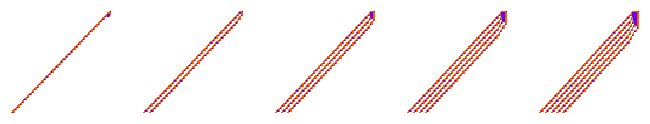
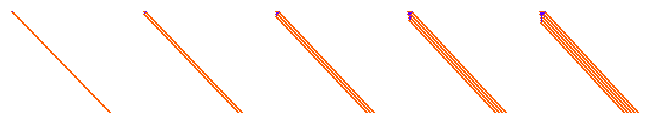
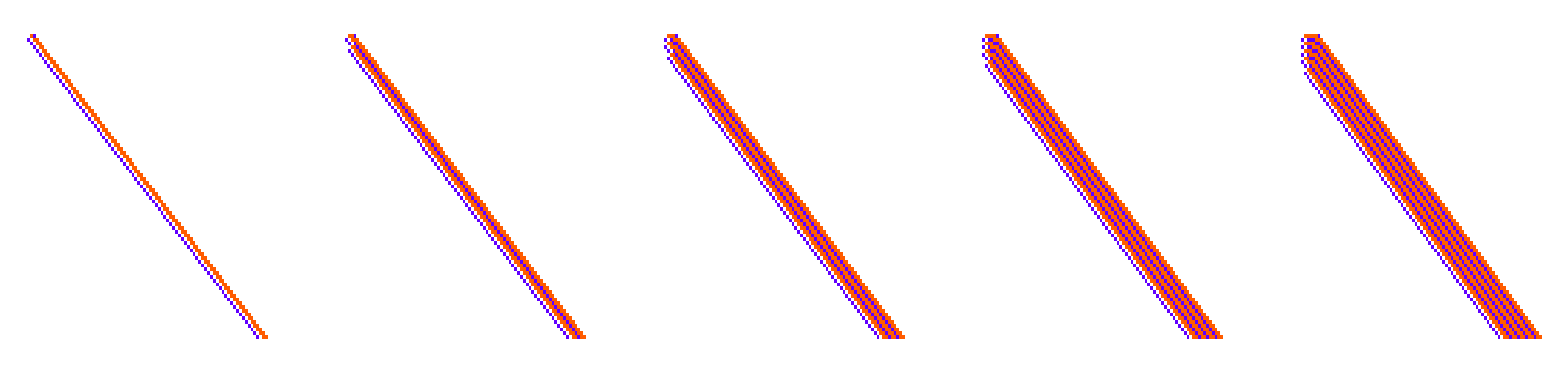
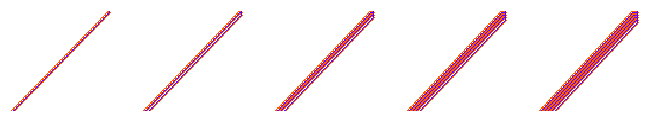
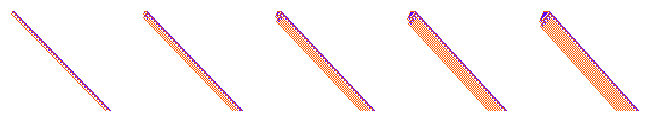
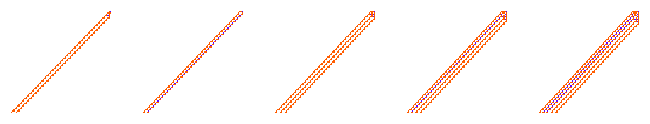
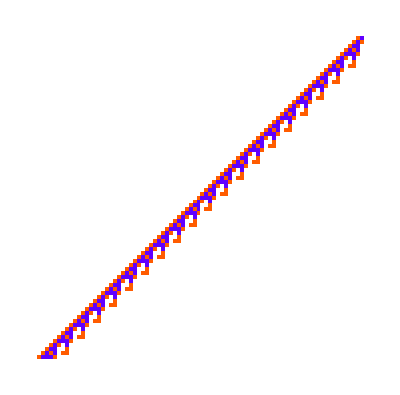
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphicsRow[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 80], {i, 5}]]&/@ Select[, #Fitness == 0&]
```

```mathematica
ParallelTable[SeedRandom[222350 + i];
AdaptiveCellularAutomaton[<|"Rule"->{0, 3, 1}, "Depth"->1000, 
"MutationFunction"->(RandomRuleMutation[#Rule, 1]&),
"FitnessFunction"-> (-Total[Abs[Table[CenterArray[#, Max[Length[#],2i]&[#]] - CenterArray[Table[1, 2i], Max[Length[#],2i]]&[CellularAutomaton[#1, {Append[Table[1, i], 2], 0}, {{{60}}}]] , {i, 5}]], 2]&)|>, "Final"], {i , 500}]
```

{<|Rule→{1457956491228,3,1},Fitness→-4|>,<|Rule→{521948864943,3,1},Fitness→-14|>,<|Rule→{4729566116745,3,1},Fitness→-9|>,<|Rule→{6577310320821,3,1},Fitness→-16|>,<|Rule→{2754117177543,3,1},Fitness→-4|>,<|Rule→{7381969329,3,1},Fitness→-5|>,<|Rule→{7095423521520,3,1},Fitness→-8|>,<|Rule→{4375395227277,3,1},Fitness→-3|>,<|Rule→{6350667543738,3,1},Fitness→-9|>,<|Rule→{5795774878311,3,1},Fitness→-5|>,<|Rule→{6464610118308,3,1},Fitness→-3|>,<|Rule→{6849964911276,3,1},Fitness→-4|>,<|Rule→{3761421401016,3,1},Fitness→-11|>,<|Rule→{6646003276626,3,1},Fitness→-14|>,<|Rule→{437562787995,3,1},Fitness→-4|>,<|Rule→{1911166477977,3,1},Fitness→-5|>,<|Rule→{4438253169054,3,1},Fitness→-4|>,<|Rule→{2857197825858,3,1},Fitness→-10|>,<|Rule→{477773522826,3,1},Fitness→-11|>,<|Rule→{3779168017878,3,1},Fitness→-15|>,<|Rule→{3405466245603,3,1},Fitness→-11|>,<|Rule→{238609742442,3,1},Fitness→-13|>,<|Rule→{7013782204029,3,1},Fitness→-3|>,<|Rule→{6123330831189,3,1},Fitness→-5|>,<|Rule→{4109953379751,3,1},Fitness→-12|>,<|Rule→{5179736023677,3,1},Fitness→-12|>,<|Rule→{3004663062699,3,1},Fitness→-19|>,<|Rule→{164473979466,3,1},Fitness→-5|>,<|Rule→{6799619206704,3,1},Fitness→-17|>,<|Rule→{2919704974791,3,1},Fitness→-4|>,<|Rule→{3233891978442,3,1},Fitness→-5|>,<|Rule→{3433338174267,3,1},Fitness→-7|>,<|Rule→{81720418158,3,1},Fitness→-10|>,<|Rule→{2313285381378,3,1},Fitness→-7|>,<|Rule→{3478853128761,3,1},Fitness→-12|>,<|Rule→{181879386633,3,1},Fitness→-9|>,<|Rule→{3594911691057,3,1},Fitness→-4|>,<|Rule→{5369152564335,3,1},Fitness→-5|>,<|Rule→{2191619298393,3,1},Fitness→-15|>,<|Rule→{3765318271560,3,1},Fitness→-10|>,<|Rule→{2076414635916,3,1},Fitness→-12|>,<|Rule→{1953906562452,3,1},Fitness→-8|>,<|Rule→{3014811970425,3,1},Fitness→-15|>,<|Rule→{7143427591245,3,1},Fitness→-13|>,<|Rule→{6152509202157,3,1},Fitness→-6|>,<|Rule→{4061360616129,3,1},Fitness→-13|>,<|Rule→{5506185224457,3,1},Fitness→-4|>,<|Rule→{3531433778856,3,1},Fitness→-10|>,<|Rule→{5497891513587,3,1},Fitness→-9|>,<|Rule→{4091647351365,3,1},Fitness→-2|>,<|Rule→{10500155646,3,1},Fitness→-12|>,<|Rule→{1229048129982,3,1},Fitness→-5|>,<|Rule→{5966627138271,3,1},Fitness→-5|>,<|Rule→{2953468020189,3,1},Fitness→-8|>,<|Rule→{4872824287677,3,1},Fitness→-6|>,<|Rule→{5609769617646,3,1},Fitness→-4|>,<|Rule→{6086267888403,3,1},Fitness→-6|>,<|Rule→{4049677741215,3,1},Fitness→-10|>,<|Rule→{5227160799600,3,1},Fitness→-3|>,<|Rule→{1385339089401,3,1},Fitness→-9|>,<|Rule→{2243363770143,3,1},Fitness→-12|>,<|Rule→{3980938033047,3,1},Fitness→-8|>,<|Rule→{3087533102355,3,1},Fitness→-4|>,<|Rule→{445804663644,3,1},Fitness→-12|>,<|Rule→{6917807710356,3,1},Fitness→-4|>,<|Rule→{6428607609678,3,1},Fitness→-12|>,<|Rule→{948580660632,3,1},Fitness→-10|>,<|Rule→{4719936516714,3,1},Fitness→-11|>,<|Rule→{7615531730520,3,1},Fitness→-9|>,<|Rule→{7168865933574,3,1},Fitness→-14|>,<|Rule→{3898762732542,3,1},Fitness→-5|>,<|Rule→{4879912532589,3,1},Fitness→-4|>,<|Rule→{892993803345,3,1},Fitness→-12|>,<|Rule→{5600514642129,3,1},Fitness→-4|>,<|Rule→{5747396006697,3,1},Fitness→-6|>,<|Rule→{2210933571648,3,1},Fitness→-9|>,<|Rule→{4307594152869,3,1},Fitness→-2|>,<|Rule→{7187293962522,3,1},Fitness→-14|>,<|Rule→{4747343099346,3,1},Fitness→-6|>,<|Rule→{6086915551692,3,1},Fitness→-7|>,<|Rule→{6243027988065,3,1},Fitness→-10|>,<|Rule→{6317212320981,3,1},Fitness→-11|>,<|Rule→{6140293498665,3,1},Fitness→-10|>,<|Rule→{6712511816475,3,1},Fitness→-6|>,<|Rule→{127176622785,3,1},Fitness→-3|>,<|Rule→{2373669832353,3,1},Fitness→-5|>,<|Rule→{3660190167825,3,1},Fitness→-14|>,<|Rule→{3892860664245,3,1},Fitness→-6|>,<|Rule→{7364198198448,3,1},Fitness→-14|>,<|Rule→{3468313056714,3,1},Fitness→-9|>,<|Rule→{1742551712697,3,1},Fitness→-10|>,<|Rule→{4447479047025,3,1},Fitness→-5|>,<|Rule→{2572751484849,3,1},Fitness→-5|>,<|Rule→{304964302203,3,1},Fitness→-6|>,<|Rule→{6111340028697,3,1},Fitness→-3|>,<|Rule→{3074003847153,3,1},Fitness→-12|>,<|Rule→{3549081990435,3,1},Fitness→-4|>,<|Rule→{4733458013502,3,1},Fitness→-4|>,<|Rule→{3958239189744,3,1},Fitness→-4|>,<|Rule→{5388313508694,3,1},Fitness→-15|>,<|Rule→{2450584817868,3,1},Fitness→-5|>,<|Rule→{1166297053836,3,1},Fitness→-8|>,<|Rule→{5832747566361,3,1},Fitness→-14|>,<|Rule→{872859201402,3,1},Fitness→-15|>,<|Rule→{307302765165,3,1},Fitness→-17|>,<|Rule→{2209471989294,3,1},Fitness→-6|>,<|Rule→{4984329634263,3,1},Fitness→-4|>,<|Rule→{6647424952848,3,1},Fitness→-5|>,<|Rule→{992181539565,3,1},Fitness→-6|>,<|Rule→{4491544917951,3,1},Fitness→-9|>,<|Rule→{4884375030030,3,1},Fitness→-4|>,<|Rule→{3228008545164,3,1},Fitness→-5|>,<|Rule→{3844889832114,3,1},Fitness→-9|>,<|Rule→{6437141180424,3,1},Fitness→-14|>,<|Rule→{3202568052870,3,1},Fitness→-5|>,<|Rule→{5237502030930,3,1},Fitness→-15|>,<|Rule→{5831370543954,3,1},Fitness→-11|>,<|Rule→{7494275175792,3,1},Fitness→-9|>,<|Rule→{6412648123689,3,1},Fitness→-4|>,<|Rule→{6340631435505,3,1},Fitness→-6|>,<|Rule→{3647335155819,3,1},Fitness→-9|>,<|Rule→{1037184656937,3,1},Fitness→-11|>,<|Rule→{5097879237276,3,1},Fitness→-9|>,<|Rule→{3870624117135,3,1},Fitness→-2|>,<|Rule→{6514110668349,3,1},Fitness→-11|>,<|Rule→{4022782070337,3,1},Fitness→-10|>,<|Rule→{5036995458639,3,1},Fitness→-12|>,<|Rule→{5585980866462,3,1},Fitness→-8|>,<|Rule→{4756316023530,3,1},Fitness→-4|>,<|Rule→{75223993842,3,1},Fitness→-13|>,<|Rule→{4856409334107,3,1},Fitness→-5|>,<|Rule→{5873456822007,3,1},Fitness→-9|>,<|Rule→{4667089500126,3,1},Fitness→-5|>,<|Rule→{457068770415,3,1},Fitness→-15|>,<|Rule→{1620744491313,3,1},Fitness→-4|>,<|Rule→{5768851107249,3,1},Fitness→-4|>,<|Rule→{1161838410840,3,1},Fitness→-5|>,<|Rule→{5547973723272,3,1},Fitness→-4|>,<|Rule→{1836747452646,3,1},Fitness→-12|>,<|Rule→{6040803486042,3,1},Fitness→-5|>,<|Rule→{2984772487848,3,1},Fitness→-6|>,<|Rule→{157572633609,3,1},Fitness→-10|>,<|Rule→{6923187331371,3,1},Fitness→-2|>,<|Rule→{6409333788048,3,1},Fitness→-10|>,<|Rule→{4416101950371,3,1},Fitness→-19|>,<|Rule→{21458292726,3,1},Fitness→-5|>,<|Rule→{22620271350,3,1},Fitness→-5|>,<|Rule→{6645494987865,3,1},Fitness→-11|>,<|Rule→{3990452066274,3,1},Fitness→-5|>,<|Rule→{2907408548052,3,1},Fitness→-5|>,<|Rule→{3792672442845,3,1},Fitness→-8|>,<|Rule→{2978266289274,3,1},Fitness→-4|>,<|Rule→{3612358367592,3,1},Fitness→-10|>,<|Rule→{5695269385926,3,1},Fitness→-7|>,<|Rule→{1080050565603,3,1},Fitness→-9|>,<|Rule→{6975268824018,3,1},Fitness→-5|>,<|Rule→{3811084533420,3,1},Fitness→-7|>,<|Rule→{6447793583709,3,1},Fitness→-6|>,<|Rule→{7243529559375,3,1},Fitness→-10|>,<|Rule→{5550475211946,3,1},Fitness→-3|>,<|Rule→{6988182493323,3,1},Fitness→-5|>,<|Rule→{2076926252931,3,1},Fitness→-11|>,<|Rule→{3440841417738,3,1},Fitness→-4|>,<|Rule→{4130124648417,3,1},Fitness→-9|>,<|Rule→{3519652601472,3,1},Fitness→-8|>,<|Rule→{956092318083,3,1},Fitness→-13|>,<|Rule→{3774306683808,3,1},Fitness→-8|>,<|Rule→{473707321491,3,1},Fitness→-5|>,<|Rule→{2549333756181,3,1},Fitness→-5|>,<|Rule→{3811399318656,3,1},Fitness→-10|>,<|Rule→{2287596179685,3,1},Fitness→-15|>,<|Rule→{3180027886722,3,1},Fitness→-9|>,<|Rule→{1268729128392,3,1},Fitness→-14|>,<|Rule→{2998413997695,3,1},Fitness→-11|>,<|Rule→{4908767876598,3,1},Fitness→-5|>,<|Rule→{292411900140,3,1},Fitness→-8|>,<|Rule→{7472364151548,3,1},Fitness→-10|>,<|Rule→{7246047166884,3,1},Fitness→-4|>,<|Rule→{7574938734834,3,1},Fitness→-5|>,<|Rule→{6754295806326,3,1},Fitness→-9|>,<|Rule→{600403524255,3,1},Fitness→-6|>,<|Rule→{5710548368031,3,1},Fitness→-9|>,<|Rule→{1963217760261,3,1},Fitness→-10|>,<|Rule→{6338741683302,3,1},Fitness→-15|>,<|Rule→{6412791846051,3,1},Fitness→-6|>,<|Rule→{855015414669,3,1},Fitness→-6|>,<|Rule→{62958471933,3,1},Fitness→-7|>,<|Rule→{7336689577884,3,1},Fitness→-6|>,<|Rule→{3754442858220,3,1},Fitness→-14|>,<|Rule→{4878235845765,3,1},Fitness→-14|>,<|Rule→{6949540827912,3,1},Fitness→-2|>,<|Rule→{2602528747236,3,1},Fitness→-14|>,<|Rule→{6259307220297,3,1},Fitness→-8|>,<|Rule→{1550052583056,3,1},Fitness→-5|>,<|Rule→{4773497785446,3,1},Fitness→-8|>,<|Rule→{4681037991717,3,1},Fitness→-4|>,<|Rule→{3526724496255,3,1},Fitness→-4|>,<|Rule→{1802981095341,3,1},Fitness→-11|>,<|Rule→{5120052528540,3,1},Fitness→-9|>,<|Rule→{1638201034179,3,1},Fitness→-14|>,<|Rule→{510504007044,3,1},Fitness→-6|>,<|Rule→{3898260640191,3,1},Fitness→-12|>,<|Rule→{4598639056182,3,1},Fitness→-15|>,<|Rule→{370012798953,3,1},Fitness→-3|>,<|Rule→{3117909738906,3,1},Fitness→-6|>,<|Rule→{3388659022533,3,1},Fitness→-6|>,<|Rule→{6511555614510,3,1},Fitness→-4|>,<|Rule→{2770218300495,3,1},Fitness→-10|>,<|Rule→{1172795463285,3,1},Fitness→-6|>,<|Rule→{3940316653446,3,1},Fitness→-9|>,<|Rule→{6169539263277,3,1},Fitness→-5|>,<|Rule→{2360874477339,3,1},Fitness→-11|>,<|Rule→{3704542362879,3,1},Fitness→-4|>,<|Rule→{1582811365914,3,1},Fitness→-14|>,<|Rule→{2419270627428,3,1},Fitness→-15|>,<|Rule→{4636971494217,3,1},Fitness→-10|>,<|Rule→{3904738546950,3,1},Fitness→-5|>,<|Rule→{5944109312685,3,1},Fitness→-8|>,<|Rule→{123607938603,3,1},Fitness→-5|>,<|Rule→{5766655851072,3,1},Fitness→-3|>,<|Rule→{5819751782241,3,1},Fitness→-14|>,<|Rule→{2455965610980,3,1},Fitness→-4|>,<|Rule→{1326658557300,3,1},Fitness→-12|>,<|Rule→{5612032259388,3,1},Fitness→-3|>,<|Rule→{3002734012146,3,1},Fitness→-11|>,<|Rule→{1463888109591,3,1},Fitness→-13|>,<|Rule→{5509468978713,3,1},Fitness→-14|>,<|Rule→{1294957686252,3,1},Fitness→-11|>,<|Rule→{7303098555495,3,1},Fitness→-4|>,<|Rule→{1084134947679,3,1},Fitness→-11|>,<|Rule→{7484270565153,3,1},Fitness→-7|>,<|Rule→{2200698723414,3,1},Fitness→-5|>,<|Rule→{2814502448178,3,1},Fitness→-6|>,<|Rule→{5036181946704,3,1},Fitness→-4|>,<|Rule→{6980036756193,3,1},Fitness→-7|>,<|Rule→{984745551942,3,1},Fitness→-10|>,<|Rule→{5022612362052,3,1},Fitness→-6|>,<|Rule→{1155596193993,3,1},Fitness→-15|>,<|Rule→{549689575968,3,1},Fitness→-15|>,<|Rule→{6973116867846,3,1},Fitness→-10|>,<|Rule→{2624823948627,3,1},Fitness→-4|>,<|Rule→{2498300384949,3,1},Fitness→-4|>,<|Rule→{3237163623906,3,1},Fitness→-10|>,<|Rule→{1155825558921,3,1},Fitness→-5|>,<|Rule→{2561843511390,3,1},Fitness→-9|>,<|Rule→{7072812945576,3,1},Fitness→-6|>,<|Rule→{5982898968666,3,1},Fitness→-5|>,<|Rule→{7096323238605,3,1},Fitness→-12|>,<|Rule→{2955950316087,3,1},Fitness→-4|>,<|Rule→{1165181029962,3,1},Fitness→-4|>,<|Rule→{4492764852885,3,1},Fitness→-6|>,<|Rule→{4118157821550,3,1},Fitness→-15|>,<|Rule→{3747173966766,3,1},Fitness→-10|>,<|Rule→{2205072246216,3,1},Fitness→-8|>,<|Rule→{3731436367488,3,1},Fitness→-10|>,<|Rule→{3022417288317,3,1},Fitness→-5|>,<|Rule→{4862303597556,3,1},Fitness→-15|>,<|Rule→{6872989765386,3,1},Fitness→-5|>,<|Rule→{2927983419039,3,1},Fitness→-14|>,<|Rule→{2797444346445,3,1},Fitness→-15|>,<|Rule→{6161877563184,3,1},Fitness→-6|>,<|Rule→{1649717487369,3,1},Fitness→-10|>,<|Rule→{6653520593982,3,1},Fitness→-9|>,<|Rule→{4272592503096,3,1},Fitness→-6|>,<|Rule→{2722583140857,3,1},Fitness→-9|>,<|Rule→{4299777780312,3,1},Fitness→-9|>,<|Rule→{6359333676444,3,1},Fitness→-5|>,<|Rule→{4356404230446,3,1},Fitness→-3|>,<|Rule→{171047615445,3,1},Fitness→-10|>,<|Rule→{1240541383386,3,1},Fitness→-5|>,<|Rule→{3310498068318,3,1},Fitness→-11|>,<|Rule→{990923590629,3,1},Fitness→-2|>,<|Rule→{1372216933539,3,1},Fitness→-3|>,<|Rule→{5905485650208,3,1},Fitness→-2|>,<|Rule→{5342219602455,3,1},Fitness→-5|>,<|Rule→{1936808173251,3,1},Fitness→-5|>,<|Rule→{5660411305482,3,1},Fitness→-7|>,<|Rule→{6645158177472,3,1},Fitness→-4|>,<|Rule→{3736115972745,3,1},Fitness→-12|>,<|Rule→{3569472222930,3,1},Fitness→-13|>,<|Rule→{1203632937792,3,1},Fitness→-9|>,<|Rule→{7099379402598,3,1},Fitness→-10|>,<|Rule→{1168184613180,3,1},Fitness→-3|>,<|Rule→{2944457099685,3,1},Fitness→-10|>,<|Rule→{3802454992161,3,1},Fitness→-4|>,<|Rule→{5991730911111,3,1},Fitness→-10|>,<|Rule→{3702967438761,3,1},Fitness→-12|>,<|Rule→{1332558578961,3,1},Fitness→-14|>,<|Rule→{2945156095530,3,1},Fitness→-13|>,<|Rule→{3690236542182,3,1},Fitness→-10|>,<|Rule→{6196415619834,3,1},Fitness→-12|>,<|Rule→{1606649314113,3,1},Fitness→-6|>,<|Rule→{5349055679892,3,1},Fitness→-12|>,<|Rule→{3570919377336,3,1},Fitness→-6|>,<|Rule→{6636784252089,3,1},Fitness→-6|>,<|Rule→{1288591597602,3,1},Fitness→-12|>,<|Rule→{3542625505182,3,1},Fitness→-10|>,<|Rule→{6454293282351,3,1},Fitness→-6|>,<|Rule→{2613229452192,3,1},Fitness→-4|>,<|Rule→{3702059159049,3,1},Fitness→-10|>,<|Rule→{3181375952859,3,1},Fitness→-7|>,<|Rule→{6345156205998,3,1},Fitness→-2|>,<|Rule→{4726285274052,3,1},Fitness→-13|>,<|Rule→{1631319389787,3,1},Fitness→-5|>,<|Rule→{6438524255136,3,1},Fitness→-4|>,<|Rule→{5546576603991,3,1},Fitness→-9|>,<|Rule→{5292095569608,3,1},Fitness→-10|>,<|Rule→{4760070588072,3,1},Fitness→-5|>,<|Rule→{4391647796169,3,1},Fitness→-6|>,<|Rule→{6087197749536,3,1},Fitness→-8|>,<|Rule→{2966725611162,3,1},Fitness→-13|>,<|Rule→{4086087940260,3,1},Fitness→-3|>,<|Rule→{2395868123916,3,1},Fitness→-5|>,<|Rule→{2689664100543,3,1},Fitness→-13|>,<|Rule→{3888614442681,3,1},Fitness→-16|>,<|Rule→{5288765396499,3,1},Fitness→-8|>,<|Rule→{2968901644248,3,1},Fitness→-12|>,<|Rule→{1354606383816,3,1},Fitness→-3|>,<|Rule→{3821773965846,3,1},Fitness→-15|>,<|Rule→{6533585878239,3,1},Fitness→-4|>,<|Rule→{3404646074121,3,1},Fitness→-4|>,<|Rule→{4779434276478,3,1},Fitness→-10|>,<|Rule→{5904798617925,3,1},Fitness→-15|>,<|Rule→{6384983851179,3,1},Fitness→-4|>,<|Rule→{3089814762276,3,1},Fitness→-4|>,<|Rule→{1145007824847,3,1},Fitness→-6|>,<|Rule→{4577357594250,3,1},Fitness→-7|>,<|Rule→{2424557755620,3,1},Fitness→-12|>,<|Rule→{4024929029886,3,1},Fitness→-9|>,<|Rule→{3047664039042,3,1},Fitness→-5|>,<|Rule→{5188743693948,3,1},Fitness→-5|>,<|Rule→{6632191499328,3,1},Fitness→-6|>,<|Rule→{7265863251918,3,1},Fitness→-4|>,<|Rule→{1978510539573,3,1},Fitness→-10|>,<|Rule→{6563508652620,3,1},Fitness→-16|>,<|Rule→{3142945331106,3,1},Fitness→-10|>,<|Rule→{4762548099240,3,1},Fitness→-4|>,<|Rule→{5972925336006,3,1},Fitness→-9|>,<|Rule→{1466969974884,3,1},Fitness→-12|>,<|Rule→{2402197711479,3,1},Fitness→-8|>,<|Rule→{983767917345,3,1},Fitness→-5|>,<|Rule→{7082403812370,3,1},Fitness→-8|>,<|Rule→{6440717427303,3,1},Fitness→-6|>,<|Rule→{6350027675733,3,1},Fitness→-10|>,<|Rule→{2112153527232,3,1},Fitness→-7|>,<|Rule→{6846171784542,3,1},Fitness→-6|>,<|Rule→{4912254663537,3,1},Fitness→-5|>,<|Rule→{485071367880,3,1},Fitness→-5|>,<|Rule→{7358814754581,3,1},Fitness→-5|>,<|Rule→{1905612984390,3,1},Fitness→-5|>,<|Rule→{206344395486,3,1},Fitness→-10|>,<|Rule→{300358181856,3,1},Fitness→-5|>,<|Rule→{3599559134166,3,1},Fitness→-12|>,<|Rule→{5101703534115,3,1},Fitness→-6|>,<|Rule→{6256691885160,3,1},Fitness→-10|>,<|Rule→{434402656236,3,1},Fitness→-10|>,<|Rule→{5815970437833,3,1},Fitness→-10|>,<|Rule→{4663995759711,3,1},Fitness→-10|>,<|Rule→{1185558635031,3,1},Fitness→-10|>,<|Rule→{3552715548135,3,1},Fitness→-13|>,<|Rule→{7455411544035,3,1},Fitness→-5|>,<|Rule→{1544196198102,3,1},Fitness→-6|>,<|Rule→{1876384489026,3,1},Fitness→-5|>,<|Rule→{5034354493329,3,1},Fitness→-4|>,<|Rule→{6511034736777,3,1},Fitness→-10|>,<|Rule→{5233815640473,3,1},Fitness→-11|>,<|Rule→{7446155802858,3,1},Fitness→-10|>,<|Rule→{2222667368766,3,1},Fitness→-4|>,<|Rule→{3080056965720,3,1},Fitness→-4|>,<|Rule→{1361766165822,3,1},Fitness→-4|>,<|Rule→{4275448458096,3,1},Fitness→-11|>,<|Rule→{3013119246864,3,1},Fitness→-5|>,<|Rule→{7105471844661,3,1},Fitness→-8|>,<|Rule→{3978709815459,3,1},Fitness→-9|>,<|Rule→{4471954197972,3,1},Fitness→-3|>,<|Rule→{5137877298519,3,1},Fitness→-4|>,<|Rule→{5116885042149,3,1},Fitness→-5|>,<|Rule→{5328739872333,3,1},Fitness→-13|>,<|Rule→{7122976531746,3,1},Fitness→-4|>,<|Rule→{5920190811702,3,1},Fitness→-12|>,<|Rule→{463903632765,3,1},Fitness→-10|>,<|Rule→{6204589277922,3,1},Fitness→-4|>,<|Rule→{5956919228220,3,1},Fitness→-8|>,<|Rule→{2101675690050,3,1},Fitness→-9|>,<|Rule→{2954659389336,3,1},Fitness→-13|>,<|Rule→{990775632537,3,1},Fitness→-12|>,<|Rule→{4691087712900,3,1},Fitness→-13|>,<|Rule→{774589909059,3,1},Fitness→-5|>,<|Rule→{6695952596679,3,1},Fitness→-2|>,<|Rule→{6245302268889,3,1},Fitness→-13|>,<|Rule→{5222535665355,3,1},Fitness→-6|>,<|Rule→{601003087464,3,1},Fitness→-10|>,<|Rule→{7192262741724,3,1},Fitness→-2|>,<|Rule→{5634687724062,3,1},Fitness→-13|>,<|Rule→{2057560995876,3,1},Fitness→-17|>,<|Rule→{1263473065425,3,1},Fitness→-12|>,<|Rule→{4289929645395,3,1},Fitness→-4|>,<|Rule→{5590752843324,3,1},Fitness→-15|>,<|Rule→{270393099417,3,1},Fitness→-13|>,<|Rule→{3221206866543,3,1},Fitness→-6|>,<|Rule→{2017712560194,3,1},Fitness→-10|>,<|Rule→{1606617400140,3,1},Fitness→-19|>,<|Rule→{5464327265463,3,1},Fitness→-11|>,<|Rule→{6734511829035,3,1},Fitness→-8|>,<|Rule→{201660904026,3,1},Fitness→-16|>,<|Rule→{4176014736297,3,1},Fitness→-13|>,<|Rule→{3439285819080,3,1},Fitness→-14|>,<|Rule→{3109501108389,3,1},Fitness→-5|>,<|Rule→{4608206559054,3,1},Fitness→-12|>,<|Rule→{5737589642727,3,1},Fitness→-10|>,<|Rule→{3468151206045,3,1},Fitness→-14|>,<|Rule→{3683650227171,3,1},Fitness→-6|>,<|Rule→{559275980355,3,1},Fitness→-12|>,<|Rule→{2007892055514,3,1},Fitness→-5|>,<|Rule→{2404904231253,3,1},Fitness→-9|>,<|Rule→{4585316466663,3,1},Fitness→-13|>,<|Rule→{992814431247,3,1},Fitness→-9|>,<|Rule→{3216558592899,3,1},Fitness→-6|>,<|Rule→{4459976759019,3,1},Fitness→-2|>,<|Rule→{4082103989829,3,1},Fitness→-3|>,<|Rule→{2140132466907,3,1},Fitness→-6|>,<|Rule→{6059627192637,3,1},Fitness→-4|>,<|Rule→{4887602883246,3,1},Fitness→-2|>,<|Rule→{6448893291888,3,1},Fitness→-5|>,<|Rule→{3877647454161,3,1},Fitness→-6|>,<|Rule→{5651509994859,3,1},Fitness→-4|>,<|Rule→{2636576999904,3,1},Fitness→-8|>,<|Rule→{5402437062951,3,1},Fitness→-7|>,<|Rule→{6068743328970,3,1},Fitness→-4|>,<|Rule→{2933695837962,3,1},Fitness→-10|>,<|Rule→{7576153344414,3,1},Fitness→-6|>,<|Rule→{4739262708867,3,1},Fitness→-6|>,<|Rule→{3300889780272,3,1},Fitness→-8|>,<|Rule→{2723494323573,3,1},Fitness→-14|>,<|Rule→{4601959789482,3,1},Fitness→-4|>,<|Rule→{2772103556763,3,1},Fitness→-5|>,<|Rule→{7062568112250,3,1},Fitness→-6|>,<|Rule→{1399681769400,3,1},Fitness→-11|>,<|Rule→{2102768913714,3,1},Fitness→-10|>,<|Rule→{3961225318446,3,1},Fitness→-12|>,<|Rule→{3725757546564,3,1},Fitness→-6|>,<|Rule→{6273293683554,3,1},Fitness→-2|>,<|Rule→{5990577006096,3,1},Fitness→-8|>,<|Rule→{4627572949575,3,1},Fitness→-4|>,<|Rule→{681411192831,3,1},Fitness→-11|>,<|Rule→{6496402890861,3,1},Fitness→-9|>,<|Rule→{4494642898017,3,1},Fitness→-11|>,<|Rule→{3158345336652,3,1},Fitness→-5|>,<|Rule→{3235068085656,3,1},Fitness→-5|>,<|Rule→{703778255586,3,1},Fitness→-9|>,<|Rule→{469346042580,3,1},Fitness→-13|>,<|Rule→{6295359993435,3,1},Fitness→-8|>,<|Rule→{5036216295045,3,1},Fitness→-6|>,<|Rule→{990961947855,3,1},Fitness→-6|>,<|Rule→{3624408668382,3,1},Fitness→-6|>,<|Rule→{2672114211063,3,1},Fitness→-12|>,<|Rule→{5123743156893,3,1},Fitness→-5|>,<|Rule→{1208530122543,3,1},Fitness→-12|>,<|Rule→{6363958089879,3,1},Fitness→-2|>,<|Rule→{5710379142144,3,1},Fitness→-9|>,<|Rule→{7481087486262,3,1},Fitness→-3|>,<|Rule→{3059131233495,3,1},Fitness→-7|>,<|Rule→{4660192988154,3,1},Fitness→-10|>,<|Rule→{6345570858498,3,1},Fitness→-15|>,<|Rule→{6262703138241,3,1},Fitness→-8|>,<|Rule→{132992537880,3,1},Fitness→-5|>,<|Rule→{4148115017403,3,1},Fitness→-8|>,<|Rule→{1145364908538,3,1},Fitness→-5|>,<|Rule→{3319956524190,3,1},Fitness→-5|>,<|Rule→{6147609534714,3,1},Fitness→-5|>,<|Rule→{3199081686858,3,1},Fitness→-6|>,<|Rule→{639718780761,3,1},Fitness→-15|>,<|Rule→{3900920162292,3,1},Fitness→-1|>,<|Rule→{1762425955422,3,1},Fitness→-4|>,<|Rule→{6328922307537,3,1},Fitness→-5|>,<|Rule→{6024067524171,3,1},Fitness→-10|>,<|Rule→{515420130861,3,1},Fitness→-6|>,<|Rule→{3261846575127,3,1},Fitness→-6|>,<|Rule→{4703791564152,3,1},Fitness→-10|>,<|Rule→{6814967993379,3,1},Fitness→-4|>,<|Rule→{3221107380783,3,1},Fitness→-9|>,<|Rule→{5770003690758,3,1},Fitness→-5|>,<|Rule→{4844551624314,3,1},Fitness→-6|>,<|Rule→{6754579216572,3,1},Fitness→-9|>,<|Rule→{6957978699006,3,1},Fitness→-4|>,<|Rule→{4797182755539,3,1},Fitness→-5|>,<|Rule→{6245278289001,3,1},Fitness→-4|>,<|Rule→{4251002598180,3,1},Fitness→-9|>,<|Rule→{3431251244301,3,1},Fitness→-3|>,<|Rule→{6028333756686,3,1},Fitness→-9|>,<|Rule→{1624772542383,3,1},Fitness→-12|>,<|Rule→{7204963470660,3,1},Fitness→-12|>,<|Rule→{3711291726888,3,1},Fitness→-11|>,<|Rule→{7293790785231,3,1},Fitness→-4|>,<|Rule→{3310701647769,3,1},Fitness→-6|>,<|Rule→{4830416352408,3,1},Fitness→-10|>,<|Rule→{5661784343070,3,1},Fitness→-6|>,<|Rule→{5243427207921,3,1},Fitness→-5|>,<|Rule→{504876278217,3,1},Fitness→-8|>,<|Rule→{4313402682780,3,1},Fitness→-2|>}

```mathematica
ListLinePlot[Join[{Table[ 2i, {i, 50}]}, Tooltip[Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}], ArrayPlot[CellularAutomaton[#Rule,{Append[Table[1, 15], 2], 0},60]]]&/@ ], PlotHighlighting->None, PlotStyle->Prepend[Table[Orange, 200], Blue], Frame->True, FrameLabel->{"Input", "Output"}, AspectRatio->.4, PlotRange->All]
```

-Graphics-

```mathematica
Row[Table[With[{ca = CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 20]},Show[ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2]],
Graphics[{Line[{{0, Length[ca]},{0, Length[ca] + 1}}],Line[{{0 + i, Length[ca]},{0 + i, Length[ca] + 1}}], Style[Text[ToString[i], {i /2, Length[ca] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[ca]], 1]),
Style[Text[ToString[Count[Last[ca], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[ca]], 1]], -2}],10]
}], PlotRange->All]], {i, 8}]&@ SelectFirst[, #Fitness>-2&]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Show[ Mesh->True, MeshStyle->Opacity[.3], "ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, "InitialIndex"->0, ImageSize->175,
Frame->False,
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],FrameTicks->{False,  False, False,({{1 + #,"", {-.01, .05}}, {5 + #, "", {-.01, .05}}}&[4.5])}], Graphics[Text["4", {7, Length[ca] + 1}]], Frame->True, PlotRangePadding->{{Automatic, Automatic}, {Automatic, -.75}}]
```

```mathematica
Row[Table[With[{ca = CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 40]},Show[ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2]],
Graphics[{Line[{{0, Length[ca]},{0, Length[ca] + 1}}],Line[{{0 + i, Length[ca]},{0 + i, Length[ca] + 1}}], Style[Text[ToString[i], {i /2, Length[ca] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[ca]], 1]),
Style[Text[ToString[Count[Last[ca], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[ca]], 1]], -2}],10]
}], PlotRange->All]], {i, 20}]&@ runs[[]][[6]]]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[Table[With[{ca = CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 40]},Show[ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2]],
Graphics[{Line[{{0, Length[ca]},{0, Length[ca] + 1}}],Line[{{0 + i, Length[ca]},{0 + i, Length[ca] + 1}}], Style[Text[ToString[i], {i /2, Length[ca] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[ca]], 1]),
Style[Text[ToString[Count[Last[ca], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[ca]], 1]], -2}],10]
}], PlotRange->All]], {i, 10}]&/@ {<|"Rule"->{413800411809,3,1},"Fitness"->-2|>,<|"Rule"->{3135859809879,3,1},"Fitness"->-2|>,<|"Rule"->{3508894595580,3,1},"Fitness"->-2|>,<|"Rule"->{5546573670615,3,1},"Fitness"->-9|>,<|"Rule"->{36166577667,3,1},"Fitness"->-9|>}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Row[Table[With[{ca = CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 16]},Show[ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2]],
Graphics[{Line[{{0, Length[ca]},{0, Length[ca] + 1}}],Line[{{0 + i, Length[ca]},{0 + i, Length[ca] + 1}}], Style[Text[ToString[i], {i /2, Length[ca] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[ca]], 1]),
Style[Text[ToString[Count[Last[ca], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[ca]], 1]], -2}],10]
}], PlotRange->All]], {i, 8}]&/@ {[[74, -1]]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
[[{160, 169}, -1]]
```

{0,-13}

```mathematica
Row[Table[With[{ca = CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0}, 30]},Show[ArrayPlot[ca, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99],4->RGBColor[0, 0.56, 0],5->RGBColor[0, 0.56, 1]}, 
FrameTicksStyle->Directive[Thickness[.01], GrayLevel[.3]],Mesh->True, MeshStyle->Opacity[.2]],
Graphics[{Line[{{0, Length[ca]},{0, Length[ca] + 1}}],Line[{{0 + i, Length[ca]},{0 + i, Length[ca] + 1}}], Style[Text[ToString[i], {i /2, Length[ca] + 2}],10],
Sequence@@(Line[{{#, 0}, {#, -1}}]&/@MapAt[# -1&, nonzeroRange[Last[ca]], 1]),
Style[Text[ToString[Count[Last[ca], 1]], {Mean[MapAt[# -1&, nonzeroRange[Last[ca]], 1]], -2}],10]
}], PlotRange->All]], {i, 8}]&/@ [[{160, 169}]]]
```

MapAt::partw: Part {1} of {} does not exist.

MapAt::psl: Position specification Line[{{1,0},{1,-1}}] in MapAt[Line[{{#1-1&,0},{#1-1&,-1}}],Line[{{{},0},{{},-1}}],Line[{{1,0},{1,-1}}]] is not a machine-sized integer or a list of machine-sized integers.

MapAt::partw: Part {1} of {} does not exist.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Abs[(Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]) - Table[ 2i, {i, 50}]]&/@ runs[[;;1]]
```

{{1,2,1,0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46}}

```mathematica
TakeSmallestBy[runs, Total[Abs[(Count[#, 1]&/@Table[CellularAutomaton[#Rule,{Append[Table[1, i], 2], 0},{{{200}}}], {i, 50}]) - Table[ 2i, {i, 50}]]]&, 5]
```

{<|Rule→{413800411809,3,1},Fitness→-2|>,<|Rule→{3135859809879,3,1},Fitness→-2|>,<|Rule→{3508894595580,3,1},Fitness→-2|>,<|Rule→{5546573670615,3,1},Fitness→-9|>,<|Rule→{36166577667,3,1},Fitness→-9|>}

```mathematica
[[74, -1]]
```

Part::partd: Part specification Null⟦74,-1⟧ is longer than depth of object.

Null⟦74,-1⟧